# GTDI - 20250907

## Functions

## Auxiliaries

### Constants

```mathematica
scPermutationStream={{2,1},{3,2},{1,3},{3,1},{1,2},{2,3}};
scPermutationArm={{3,2},{1,3},{2,1},{2,3},{3,1},{1,2}};
```

```mathematica
scPermutationSignedStream=Flatten[Table[{j,i},{i,{1,-1}},{j,scPermutationStream}],1];
scPermutationSignedArm=Flatten[Table[{j,i},{i,{1,-1}},{j,scPermutationArm}],1];
```

```mathematica
numberMark1={"1","2","3","1'","2'","3'"};
numberMark2={"OverBar[1]","OverBar[2]","OverBar[3]","OverBar[1]'","OverBar[2]'","OverBar[3]'"};
numberMark3a={"-1","-2","-3","-1'","-2'","-3'"};
numberMark3b=numberMark3a[[{4,5,6,1,2,3}]];
```

```mathematica
polynomialSymbol={x,y,z,l,m,n};
```

### Rules

```mathematica
scPermutationToZeroRule=Thread[scPermutationStream->Table[0,{6}]];
scSignedPermutationToZeroRule=Thread[scPermutationSignedStream->Table[0,{12}]];
scSignedPermutationToEmptySetRule=Thread[scPermutationSignedStream->Table[{},{12}]];
```

```mathematica
scToStreamRule=Thread[scPermutationStream->(Subscript[η,#]&/@numberMark1)];
```

```mathematica
scToSignedStreamRule=Module[{stream=Subscript[η,#]&/@numberMark1},Thread[scPermutationSignedStream->Join[stream,-stream]]];
```

```mathematica
scToArmRule=Thread[scPermutationArm->numberMark1];
```

```mathematica
scToStreamDelayRule=Thread[scPermutationSignedArm->Join[numberMark1,numberMark2]];
```

```mathematica
indexRule1=Thread[numberMark3a->numberMark2]
scToIndexRule=Thread[scPermutationSignedArm->Join[numberMark1,numberMark3b]]
```

{-1→OverBar[1],-2→OverBar[2],-3→OverBar[3],-1'→OverBar[1]',-2'→OverBar[2]',-3'→OverBar[3]'}

{{{3,2},1}→1,{{1,3},1}→2,{{2,1},1}→3,{{2,3},1}→1',{{3,1},1}→2',{{1,2},1}→3',{{3,2},-1}→-1',{{1,3},-1}→-2',{{2,1},-1}→-3',{{2,3},-1}→-1,{{3,1},-1}→-2,{{1,2},-1}→-3}

```mathematica
streamDelayToPolynomialSymbolRule=Thread[Join[numberMark1,numberMark2]->Join[polynomialSymbol,1/polynomialSymbol]];
```

```mathematica
scToPolynomialSymbolRule=scToStreamDelayRule/.streamDelayToPolynomialSymbolRule;
```

```mathematica
polynomialSymbolSwitchRule=Thread[{l,m,n}->{x,y,z}];
```

### Auxiliary functions

```mathematica
toTrueSc[i_]:=Mod[i,3]+1;
```

```mathematica
pathToSc[path_List]:={toTrueSc/@path[[All,1]],Differences@path[[All,2]]};
```

```mathematica
pointSymmetrySwitch[{sc_,t_}]:={-sc,t};
scSymmetrySwitch[{a_Integer,b_}]:={a,b}/.{2->3,3->2};
scSymmetrySwitch[{a_List,b_}]:={a/.{2->3,3->2},b};
```

```mathematica
scToStream[sc_,dt_]:=Block[{sc1=Partition[sc,2,1],stream},stream=Table[If[dt[[i]]==-1,Reverse[sc1[[i]]],sc1[[i]]],{i,Length[dt]}];Transpose[{stream,-dt}]];
```

```mathematica
dtToDelayIndex[dt_]:=Block[{delayIndex=Prepend[Table[Range[i],{i,Length[dt]-1}],{}]},Table[AppendTo[delayIndex[[i]],i],{i,Flatten[Position[dt,1]]}];delayIndex];
```

```mathematica
scToStreamAndDelay[sc_,dt_]:=Block[{stream,delay,delayIndex,delays},stream=delay=scToStream[sc,dt];delayIndex=dtToDelayIndex[dt];delays=delay[[#]]&/@delayIndex;{stream,delays}];
```

```mathematica
pathToStreamAndDelay[path_List]:=scToStreamAndDelay@@pathToSc[path];
```

```mathematica
markFromIndex[{n_,g_,i1_}]:=Subscript[GC, ToString[i1]]^(ToString[n]<>", "<>ToString[g])
markFromIndex[{n_,g_,i1_},{i2_,i3_,i4_,i5_}]:=Subscript[GC, ToString[i1]<>","<>ToString[i2]<>","<>ToString[i3]<>","<>ToString[i4]<>","<>ToString[i5]]^(ToString[n]<>","<>ToString[g])
markFromIndex[{n_,g_,i1_},"SF"]:=Subscript[GC, ToString[i1]]^(ToString[n]<>","<>ToString[g]<>",SF")
```

```mathematica
labelFromIndex[{n_,g_,i1_}]:=Style[markFromIndex[{n,g,i1}],Black,FontFamily->"Times",FontSize->14]
labelFromIndex[{n_,g_,i1_},{i2_,i3_,i4_,i5_}]:=Style[markFromIndex[{n,g,i1},{i2,i3,i4,i5}],Black,FontFamily->"Times",FontSize->14]
labelFromIndex[{n_,g_,i1_},"SF"]:=Style[markFromIndex[{n,g,i1},"SF"],Black,FontFamily->"Times",FontSize->14]
```

## Major functions

### TDI transformation

```mathematica
pathJoin[{path1_,path2_}]/;path1[[-1]]==path2[[-1]]:=Join[path1,Rest@Reverse@path2];
```

```mathematica
pathPartition[path_]/;path[[1]]==path[[-1]]:=Block[{n},n=(Length[path]+1)/2;{path[[1;;n]],path[[-1;;-n;;-1]]}];
```

```mathematica
pathZero[{path1_,path2_}]:=Sort@Cases[Most@pathJoin[{path1,path2}],{_,0}]
```

```mathematica
pathZeroPosition[{path1_,path2_}]:=Union@Flatten[Position[Most@pathJoin[{path1,path2}],#]&/@pathZero[{path1,path2}]];
```

```mathematica
pathTransform["reverse"][{path1_,path2_}]:=Reverse[{path1,path2}];
```

```mathematica
pathTransform["scSymmetry"][{path1_,path2_}]:=pathTransform["reverse"]@Map[pointSymmetrySwitch,{path1,path2},{2}];
```

```mathematica
pathTransform["rotateLeft",n_][{path1_,path2_}]:=Block[{path,pn},path=Most@pathJoin[{path1,path2}];pn=Length[path1]-1;path=RotateLeft[path,n];path=Append[path,path[[1]]];pathPartition[path]];
```

```mathematica
pathTransform["initialPointAndDirection"][{path1_,path2_}]:=Block[{sc0,dsc,path},sc0=path1[[1,1]];path=Map[#-{sc0,0}&,{path1,path2},{2}];dsc=path1[[2,1]]-path1[[1,1]];If[dsc==1,path,Reverse@path]];
```

```mathematica
pathTransform["rotateLeftPath"][{path1_,path2_}]:=Block[{index,pathSet},index=(Rest@pathZeroPosition[{path1,path2}])-1;pathSet=Table[pathTransform["rotateLeft",i][{path1,path2}],{i,index}];pathTransform["initialPointAndDirection"]/@pathSet];
```

```mathematica
pathTransform["equivalentPath"][{path1_,path2_}]:=Block[{path={path1,path2},pathS,pathR,pathSR},pathS=pathTransform["scSymmetry"]@path;{pathR,pathSR}=pathTransform["rotateLeftPath"]/@{path,pathS};Join[{pathS},pathR,pathSR]];
```

```mathematica
pathTransform["IndexRotationPath"][{path1_,path2_}]:=Block[{path={path1,path2},pathSet},pathSet={path};AppendTo[pathSet,Map[#+{1,0}&,path,{2}]];AppendTo[pathSet,Map[#-{1,0}&,path,{2}]];pathSet];
```

```mathematica
pathTransform["neededEquivalentPath"][{path1_,path2_}]:=Block[{path={path1,path2},pathS1,pathS2},pathS1=pathTransform["scSymmetry"]@path;pathS2=pathTransform["rotateLeftPath"]@pathS1;If[MemberQ[Join[{pathS1},pathS2],path],pathTransform["IndexRotationPath"]@path,Flatten[pathTransform["IndexRotationPath"]/@{path,pathS1},1]]];
```

### TDI combination format and information

#### Coordinate format

```mathematica
laserLinkTrajectoryToSc1[l_String]:=Block[{l1},l1=StringPartition[l,1];{ToExpression@l1[[1;;-1;;2]],l1[[2;;-1;;2]]/.{"←"->-1,"→"->1,"<"->-1,">"->1}}];
```

```mathematica
laserLinkTrajectoryToSc2[l_String]:=Block[{n1,l1,l2,sc1,sc2},n1=(StringLength[l]+1)/2;{l1,l2}=StringPartition[l,n1,n1-1];l2=StringReplace[StringReverse@l2,{"←"->"→","→"->"←","<"->">",">"->"<"}];laserLinkTrajectoryToSc1/@{l1,l2}];
```

```mathematica
adjustPathTime[path_List]:=Block[{m},m=Max@path[[All,All,2]];If[m>0,Map[#-{0,m}&,path,{2}],path]]
```

```mathematica
scToPath[sc_List]:=Block[{dx,d1,p0},dx=Switch[#,1,1,-2,1,-1,-1,2,-1]&/@(Differences@sc[[1]]);d1=Transpose[{dx,sc[[2]]}];p0=Switch[sc[[1,1]],1,{0,0},2,{1,0},3,{-1,0}];Accumulate@Prepend[d1,p0]]/;Depth[sc]==3;
scToPath[sc_List]:=adjustPathTime@(scToPath/@sc)/;Depth[sc]==4;
```

```mathematica
laserLinkTrajectoryToPath1[l_String]:=scToPath@laserLinkTrajectoryToSc1@l;
laserLinkTrajectoryToPath2[l_String]:=scToPath@laserLinkTrajectoryToSc2@l;
```

#### Laser link trajectory

```mathematica
pathToLaserLinkTrajectory[path_List]:=Block[{sc,dt},{sc,dt}=pathToSc[path];StringJoin@Riffle[ToString/@sc,If[#<0,"←","→"]&/@dt]];
pathToLaserLinkTrajectory[path1_List,path2_List]:=pathToLaserLinkTrajectory[Join[path1,Rest@Reverse[path2]]];
```

```mathematica
pathToLaserLinkTrajectory2[path_List]:=Block[{sc,dt},{sc,dt}=pathToSc[path];StringJoin@Riffle[ToString/@sc,If[#<0,"<",">"]&/@dt]];
pathToLaserLinkTrajectory2[path1_List,path2_List]:=pathToLaserLinkTrajectory2[Join[path1,Rest@Reverse[path2]]];
```

#### Defining formula

```mathematica
streamDelayToDelayOperator[delay_]:=If[Length[#]==0,1,Subscript["𝒟",StringJoin[#]]]&/@(delay/.scToStreamDelayRule);
```

```mathematica
pathToDelayOperatorFormula[path_List]:=Block[{stream,delay,stream1,delay1},{stream,delay}=pathToStreamAndDelay[path];stream1=stream/.scToSignedStreamRule;delay1=streamDelayToDelayOperator[delay];delay1.stream1];
pathToDelayOperatorFormula[path1_List,path2_List]:=pathToDelayOperatorFormula[path1]-pathToDelayOperatorFormula[path2];
pathToDelayOperatorFormula[path_String]:=pathToDelayOperatorFormula@@(laserLinkTrajectoryToPath2@path)
```

#### Polynomial Vector

```mathematica
pathToPolynomialVector["m1g-TDI"][path_List]:=Block[{stream,delay,v1},{stream,delay}=pathToStreamAndDelay[path];delay=Apply[Times,delay/.scToPolynomialSymbolRule,{1}];v1=scPermutationSignedStream/.Merge[Thread[stream->delay],Total]/.scSignedPermutationToZeroRule;v1[[1;;6]]-v1[[7;;12]]];
pathToPolynomialVector["m1g-TDI"][path1_List,path2_List]:=Subtract@@(pathToPolynomialVector["m1g-TDI"]/@{path1,path2});
pathToPolynomialVector["m1g-TDI"][path_String]:=pathToPolynomialVector["m1g-TDI"]@@(laserLinkTrajectoryToPath2@path);
```

```mathematica
pathToPolynomialVector["1g-TDI"][path_List]:=pathToPolynomialVector["m1g-TDI"][path]/.polynomialSymbolSwitchRule;
pathToPolynomialVector["1g-TDI"][path1_List,path2_List]:=pathToPolynomialVector["m1g-TDI"][path1,path2]/.polynomialSymbolSwitchRule;
pathToPolynomialVector["1g-TDI"][path_String]:=pathToPolynomialVector["1g-TDI"]@@(laserLinkTrajectoryToPath2@path);
```

```mathematica
pathToPolynomialVector["0g-TDI"][path_List]:=pathToPolynomialVector["1g-TDI"][path]/.{y->x,z->x};
pathToPolynomialVector["0g-TDI"][path1_List,path2_List]:=pathToPolynomialVector["1g-TDI"][path1,path2]/.{y->x,z->x};
pathToPolynomialVector["0g-TDI"][path_String]:=pathToPolynomialVector["0g-TDI"]@@(laserLinkTrajectoryToPath2@path);
```

#### Laser noise residual

```mathematica
pathToLaserNoiseIndex[p_List]/;Length[p]==1:={}
pathToLaserNoiseIndex[p_List]/;Length[p]==2:=pathToLaserNoiseIndex[p]={{toTrueSc@#[[All,1]],#[[2,2]]-#[[1,2]]}&@Reverse@p/.scToIndexRule}
pathToLaserNoiseIndex[p_List]/;Length[p]>2:=pathToLaserNoiseIndex[p]=Join[pathToLaserNoiseIndex@p[[1;;-2]],pathToLaserNoiseIndex@p[[-2;;-1]]]
```

```mathematica
pathToLaserNoiseResidual[path_List]:=Module[{index1,p1,p2,index2},index1=pathToLaserNoiseIndex/@path;{p1,p2}=Subscript["𝒟",StringJoin[#]]&/@(index1/.indexRule1);index2=toTrueSc@path[[1,-1,1]];Row[{"(",p1,"-",p2,")",Subscript[OverDot["p",1],index2]}]]
```

```mathematica
L[s_String,i_Integer]/;StringPart[s,1]=="-":=L[s,i]=-L[StringTake[s,2;;],i]
```

```mathematica
k[1,s_String]/;StringPart[s,1]=="-":=k[1,s]=L[StringTake[s,2;;],0]*L[StringTake[s,2;;],1]
k[1,s_String]:=0
k[1,s_List]/;Length[s]==1:=k[1,s]=k[1,s[[1]]]
k[1,s_List]/;Length[s]>1&&StringPart[s[[-1]],1]=="-":=k[1,s]=k[1,s[[1;;-2]]]+L[s[[-1]],1]*Sum[L[i,0],{i,s}]
k[1,s_List]/;Length[s]>1:=k[1,s]=k[1,s[[1;;-2]]]+L[s[[-1]],1]*Sum[L[i,0],{i,s[[1;;-2]]}]
k[2,s_String]:=k[2,s]=-L[s,1]
k[2,s_List]/;Length[s]==1:=k[2,s]=k[2,s[[1]]]
k[2,s_List]:=k[2,s]=k[2,s[[1;;-2]]]-L[s[[-1]],1]
```

```mathematica
bk[0,s_String]/;StringPart[s,1]=="-":=bk[0,s]=-L[StringTake[s,2;;],0]
bk[0,s_String]:=L[s,0]
bk[0,s_List]/;Length[s]==1:=bk[0,s]=bk[0,s[[1]]]
bk[0,s_List]/;Length[s]>1:=bk[0,s]=bk[0,Most@s]+L[Last@s,0]
```

```mathematica
listL0=Transpose@Table[L[i,0],{i,{"1","2","3","1'","2'","3'"}}];
coef[0,s_]:=coef[0,s]=Coefficient[bk[0,s],listL0]
coef[0,s_,0]:=(#[[1;;3]]+#[[4;;6]])&@coef[0,s]
```

```mathematica
bk[1,s_String]/;StringPart[s,1]=="-":=bk[1,s]=-L[StringTake[s,2;;],1]
bk[1,s_String]:=0
bk[1,s_List]/;Length[s]==1:=bk[1,s]=bk[1,s[[1]]]
bk[1,s_List]/;Length[s]>1&&StringPart[s[[-1]],1]=="-":=bk[1,s]=bk[1,s[[1;;-2]]]+L[s[[-1]],1]*Total@coef[0,s]
bk[1,s_List]/;Length[s]>1:=bk[1,s]=bk[1,s[[1;;-2]]]+L[s[[-1]],1]*Total@coef[0,Most@s]
```

```mathematica
listL1=Transpose@Table[L[i,1],{i,{"1","2","3","1'","2'","3'"}}];
coef[1,s_]:=coef[1,s]=Coefficient[bk[1,s],listL1]
coef[1,s_,0]:=(#[[1;;3]]+#[[4;;6]])&@coef[1,s]
```

#### Summarized information

```mathematica
informationTDI[path_String]:=Module[{p1=laserLinkTrajectoryToPath2@path,index},index=pathToLaserNoiseIndex/@p1;Echo[pathToLaserLinkTrajectory@@p1,"Laser link trajectory: "];Echo[p1,"Coordinate format: "];Echo[pathToDelayOperatorFormula/@p1,"Defining formula (two virtual optical paths): "];Echo[pathToDelayOperatorFormula@@p1//FullSimplify,"Defining formula: "];Echo[pathToLaserNoiseResidual@p1,"Laser noise residual: "];Echo[Subtract@@(coef[0,#]&/@index),"Evaluation index b for the modified first-generation TDI: "];Echo[Subtract@@(coef[1,#,0]&/@index),"Evaluation index d^0 for the second-generation TDI: "];Echo[Subtract@@(coef[1,#]&/@index),"Evaluation index d for the modified second-generation TDI: "];Echo[pathToPolynomialVector["m1g-TDI"]@@p1,"Polynomial vector format (6 variables x,y,z,l,m,n): "];Echo[pathToPolynomialVector["1g-TDI"]@@p1,"Polynomial vector format (3 variables x,y,z): "];Echo[pathToPolynomialVector["0g-TDI"]@@p1,"Polynomial vector format (1 variable x): "];]
```

### Plot

#### Spacetime diagram

```mathematica
spaceTimePlot2[{path1_List,path2_List},opts___]:=Module[{n1=Length[path1],n2=Length[path2],path1A={-1,1}*#&/@path1,path2A={-1,1}*#&/@path2,scColor={Gray,Magenta,Darker@Green},scRange,tRange,pLine1,pLine2,pLinePath1,pLinePath2,radius,pPoint,pXAxis,pYAxis,pAxisLable},{scRange,tRange}=MinMax/@Join@@@Transpose[CoordinateBounds/@{path1A,path2A}];pLine1={GrayLevel[0.7],Dashed,Thin,Line[Table[{{scRange[[1]],i},{scRange[[2]],i}},{i,tRange[[1]],tRange[[2]]}]]};pLine2=Table[{scColor[[toTrueSc[-i]]],Dashed,Line[{{i,tRange[[1]]},{i,tRange[[2]]}}]},{i,scRange[[1]],scRange[[2]]}];
pLinePath1={Red,Thickness[0.01],Line[#+{0,0.02}&/@path1A]};
pLinePath2={Darker@Blue,Thickness[0.01],Dashed,Line[#-{0,0.02}&/@path2A]};radius=0.009*(Differences[scRange][[1]]+Differences[tRange][[1]]);pPoint={FaceForm[Black],Disk[path1A[[1]],radius],Rectangle[path1A[[-1]]+{-1,-1}*radius,path1A[[-1]]+{1,1}*radius]};pXAxis={FontSize->12,Table[Text[toTrueSc[-i],{i,tRange[[1]]-0.2}],{i,scRange[[1]],scRange[[2]]}]};pYAxis={FontSize->12,Table[Text[i,{scRange[[1]]-0.2,i}],{i,tRange[[1]],tRange[[2]]}]};pAxisLable={Black,Text[Row[{Style["SC",FontFamily->"Times New Roman",FontSize->18]}],{Mean[scRange],tRange[[1]]-0.5}],Text[Row[{Style["time",FontFamily->"Times New Roman",FontSize->18]}],{scRange[[1]]-0.5,Mean[tRange]},{0,0},{0,1}]};Graphics[{pLine1,pLine2,pLinePath1,pLinePath2,pPoint,pXAxis,pYAxis,pAxisLable},opts]]
spaceTimePlot2[path1_String,opts___]:=spaceTimePlot2[laserLinkTrajectoryToPath2@path1,opts]
```

```mathematica
spaceTimePlot1[path1_List,opts___]:=Module[{n1=Length[path1],path1A={-1,1}*#&/@path1,scColor={Gray,Magenta,Darker@Green},scRange,tRange,pLine1,pLine2,pLinePath1,pLine3,radius,pPoint,pXAxis,pYAxis,pAxisLable,pPath1Lable},{scRange,tRange}=CoordinateBounds[path1A];pLine1={GrayLevel[0.7],Dashed,Thin,Line[Table[{{scRange[[1]],i},{scRange[[2]],i}},{i,tRange[[1]],tRange[[2]]}]]};pLine2=Table[{scColor[[toTrueSc[-i]]],Dashed,Line[{{i,tRange[[1]]},{i,tRange[[2]]}}]},{i,scRange[[1]],scRange[[2]]}];
pLinePath1={Red,Thick,Line[path1A]};radius=0.009*(Differences[scRange][[1]]+Differences[tRange][[1]]);pPoint={FaceForm[Black],Disk[path1A[[1]],radius],Rectangle[path1A[[-1]]+{-1,-1}*radius,path1A[[-1]]+{1,1}*radius]};pXAxis={FontSize->15,Table[Text[toTrueSc[-i],{i,tRange[[1]]-0.12}],{i,scRange[[1]],scRange[[2]]}]};pYAxis={FontSize->15,Table[Text[i,{scRange[[1]]-0.12,i}],{i,tRange[[1]],tRange[[2]]}]};pAxisLable={Black,Text[Row[{Style["SC",FontFamily->"Times New Roman",FontSize->22]}],{Mean[scRange],tRange[[1]]-0.3}],Text[Row[{Style["time",FontFamily->"Times New Roman",FontSize->22]}],{scRange[[1]]-0.35,Mean[tRange]},{0,0},{0,1}]};Graphics[{pLine1,pLine2,pLinePath1,pPoint,pXAxis,pYAxis,pAxisLable},opts]]
spaceTimePlot1[path1_String,opts___]:=spaceTimePlot1[laserLinkTrajectoryToPath1@path1,opts]
```

#### Sensitivity function diagram

```mathematica
sensitivityFunctionPlot["SF"][sf_,opts___]:=LogLogPlot[Evaluate[sf/.uReplaceRule/.parameterReplaceRule["LISA"]],{f,10^-4,1},opts,PlotRange->{Automatic,{10^-20,10^-15}},WorkingPrecision->20,Frame->True,GridLines->Automatic,AspectRatio->1,Exclusions->None]
```

```mathematica
sensitivityFunctionPlot["PV"][pv_,opts___]:=sensitivityFunctionPlot["SF"][polynomialVectorToSensitivityFunction@pv,opts]/;ArrayDepth[pv]==1;
sensitivityFunctionPlot["PV"][pv_,opts___]:=sensitivityFunctionPlot["SF"][polynomialVectorToSensitivityFunction/@pv,opts]/;ArrayDepth[pv]==2;
```

```mathematica
sensitivityFunctionPlot["path"][path_List,opts___]:=Quiet@sensitivityFunctionPlot["SF"][pathToSensitivityFunction@path,opts]/;Depth[path]==4;
sensitivityFunctionPlot["path"][path_List,opts___]:=Quiet@sensitivityFunctionPlot["SF"][pathToSensitivityFunction/@path,opts]/;Depth[path]==5;
sensitivityFunctionPlot["path"][path_List,opts___]/;Head@First@path==String:=Quiet@sensitivityFunctionPlot["SF"][pathToSensitivityFunction/@(laserLinkTrajectoryToPath2/@path),opts]
sensitivityFunctionPlot["path"][path_String,opts___]:=Quiet@sensitivityFunctionPlot["path"][laserLinkTrajectoryToPath2@path,opts]
```

### Sensitivity

#### Averaged response function (ARF)

```mathematica
aRF["f",1][u_]=4/3-2/u^2+Sin[2u]/u^3;
aRF["f",2][u_]=(-u*Cos[u]+Sin[u])/u^3-Cos[u]/3;
aRF["f",3][u_]=Log[4/3]-5/18+(-5Sin[u]+8Sin[2u]-3Sin[3u])/(8u)-(4+9Cos[u]+12Cos[2u]+Cos[3u])/(3*8u^2)+(-5Sin[u]+8Sin[2u]+5Sin[3u])/(3*8u^3)+CosIntegral[u]-2CosIntegral[2u]+CosIntegral[3u];
aRF["f",4][u_]=(-5Cos[u]+8Cos[2u]-3Cos[3u])/(8u)+(9Sin[u]+12Sin[2u]+Sin[3u])/(3*8u^2)-(8+5Cos[u]-8Cos[2u]-5Cos[3u])/(3*8u^3)-SinIntegral[u]+2SinIntegral[2u]-SinIntegral[3u];
aRF["f",5][u_]=-Log[4]+7/6+(11Sin[u]-4Sin[2u])/(4u)-(10+5Cos[u]-2Cos[2u])/(4u^2)+(5Sin[u]+4Sin[2u])/(4u^3)-2CosIntegral[u]+2CosIntegral[2u];
```

```mathematica
aRFVarRule1[vars_List]:=Thread[vars->Table[Exp[ⅈ*u],{Length@vars}]];
uReplaceRule=u->(2π*f*L)/c;
parameterReplaceRule["LISA"]={L->25*10^8,c->3*10^8,sa->3*10^(-15),sx->15*10^(-12)};
aRFSimplify[pF_]:=Refine[pF,u>0]//Simplify;
Attributes[aRFSimplify]={Listable};
```

```mathematica
polynomialVectorFourierTransform[pV_List]:=Block[{vars},vars=Union@@Variables/@pV;pV/.aRFVarRule1[vars]];
```

```mathematica
aRF["C",1][pF_List]:=Block[{value},value=Norm[#]^2&/@ComplexExpand[ExpToTrig@pF];aRFSimplify@Total@value];
aRF["C",2][pF_List]:=Block[{pFC,value1,value2,value},pFC=pF/.{Exp[xx_]:>Exp[-xx]};value1=pF[[{1,2,3}]];value2=pFC[[{5,6,4}]];value=Table[2Re@ComplexExpand@ExpToTrig[value1[[i]]*value2[[i]]],{i,3}];aRFSimplify@Total@value];
aRF["C",3][pF_List]:=Block[{pFC,value1,value2,value3,value4,value},pFC=pF/.{Exp[xx_]:>Exp[-xx]};value1=pF[[{1,2,3}]];value2=pFC[[{2,3,1}]];value3=pF[[{4,5,6}]];value4=pFC[[{6,4,5}]];
value=Table[2Re@ComplexExpand@ExpToTrig[(value1[[i]]*value2[[i]]+value3[[i]]*value4[[i]])*Exp[ⅈ*u]],{i,3}];aRFSimplify@Total@value];
aRF["C",4][pF_List]:=Block[{pFC,value1,value2,value3,value4,value},pFC=pF/.{Exp[xx_]:>Exp[-xx]};value1=pF[[{1,2,3}]];value2=pFC[[{2,3,1}]];value3=pF[[{4,5,6}]];value4=pFC[[{6,4,5}]];
value=Table[2Im@ComplexExpand@ExpToTrig[(value1[[i]]*value2[[i]]+value3[[i]]*value4[[i]])*Exp[ⅈ*u]],{i,3}];aRFSimplify@Total@value];
aRF["C",5][pF_List]:=Block[{pFC,value1,value2,value3,value},pFC=pF/.{Exp[xx_]:>Exp[-xx]};value1=pF[[{1,2,3}]];value2=pFC[[{4,5,6}]];value3=pFC[[{6,4,5}]];
value=Table[2Re@ComplexExpand@ExpToTrig[value1[[i]]*value2[[i]]+value1[[i]]*value3[[i]]],{i,3}];aRFSimplify@Total@value];
```

```mathematica
polynomialVectorToARF[pv_]:=Block[{pF,constant,cValue,fValue},pF=polynomialVectorFourierTransform[pv];constant={1/2,1,3/4,-3/4,1/4};cValue=Table[aRF["C",i][pF],{i,5}];fValue=Table[aRF["f",i][u],{i,5}];(constant*cValue).fValue//TrigReduce//Simplify];
```

```mathematica
pathToARF[path_List]:=polynomialVectorToARF@(pathToPolynomialVector["1g-TDI"]@@path);
```

#### Noise PSD

```mathematica
polynomialVectorToNoisePSD[pv_]:=Block[{pF,constant,cValue,fValue,n1,n2},pF=polynomialVectorFourierTransform[pv];constant={1,2};cValue=Table[aRF["C",i][pF],{i,2}];n1=(2L^2*sa^2)/(u^2*c^4)+(u^2*sx^2)/L^2;n2=(L^2*sa^2)/(u^2*c^4)Cos[u];(constant*cValue).{n1,n2}//TrigReduce//Simplify];
```

```mathematica
(*Backup procedure, if sa and sx are not constants*)
(*polynomialVectorToNoisePSD[pv_]:=Block[{pF,constant,cValue,fValue,c1,c2,n1,n2},pF=polynomialVectorFourierTransform[pv];constant={1,2};cValue=Table[aRF["C",i][pF],{i,2}];c1=(1+((4*10^-4*2π L)/(u c))^2)(1+((u c)/(2π L*8*10^-3))^4);c2=(1+((2*10^-3*2π L)/(u c))^4);n1=(2L^2*sa^2*c1)/(u^2*c^4)+(u^2*sx^2*c2)/L^2;n2=(L^2*sa^2*c1)/(u^2*c^4)Cos[u];(constant*cValue).{n1,n2}//TrigReduce//Simplify];*)
```

```mathematica
pathToNoisePSD[path_List]:=polynomialVectorToNoisePSD@(pathToPolynomialVector["1g-TDI"]@@path);
```

#### Sensitivity function

```mathematica
polynomialVectorToSensitivityFunction[pv_]:=Block[{arf,noisePSD},arf=polynomialVectorToARF@pv;noisePSD=polynomialVectorToNoisePSD@pv;Sqrt[(5noisePSD)/(2arf)]];
```

```mathematica
pathToSensitivityFunction[path_List]:=polynomialVectorToSensitivityFunction@(pathToPolynomialVector["1g-TDI"]@@path);
pathToSensitivityFunction[path_String]:=polynomialVectorToSensitivityFunction@(pathToPolynomialVector["1g-TDI"]@@(laserLinkTrajectoryToPath2@path));
```

```mathematica
pathToSFValue[path_,freq_]:=(pathToSensitivityFunction@path)/.uReplaceRule/.parameterReplaceRule["LISA"]/.{f->freq}//N
```

### Equivalent TDI combination

#### Generate equivalent TDI combination

```mathematica
pathTransform["allEquivalentPath"][{path1_,path2_}]:=Block[{path={path1,path2},pathSet,n=2(Length[path1]-1)-1},pathSet={path,Reverse@path};pathSet=Flatten[{#,Map[pointSymmetrySwitch,#,{2}]}&/@pathSet,1];pathSet=Flatten[{#,Map[#+{1,0}&,#,{2}],Map[#-{1,0}&,#,{2}]}&/@pathSet,1];pathSet=Flatten[Table[pathTransform["rotateLeft",i][#],{i,0,n}]&/@pathSet,1];pathToLaserLinkTrajectory@@@pathSet];
pathTransform["allEquivalentPath"][path_String]:=pathTransform["allEquivalentPath"]@laserLinkTrajectoryToPath2@path;
```

```mathematica
pathTransform["allEquivalentPath2"][{path1_,path2_}]:=Block[{path={path1,path2},pathSet,n=2(Length[path1]-1)-1},pathSet={{{0},path},{{1},Reverse@path}};pathSet=Flatten[{{Append[#[[1]],0],#[[2]]},{Append[#[[1]],1],Map[pointSymmetrySwitch,#[[2]],{2}]}}&/@pathSet,1];pathSet=Flatten[{{Append[#[[1]],0],#[[2]]},{Append[#[[1]],1],Map[#+{1,0}&,#[[2]],{2}]},{Append[#[[1]],2],Map[#-{1,0}&,#[[2]],{2}]}}&/@pathSet,1];pathSet=Flatten[Table[{Append[#[[1]],i],pathTransform["rotateLeft",i][#[[2]]]},{i,0,n}]&/@pathSet,1];{#[[1]],pathToLaserLinkTrajectory@@#[[2]]}&/@pathSet];
pathTransform["allEquivalentPath2"][path_String]:=pathTransform["allEquivalentPath2"]@laserLinkTrajectoryToPath2@path;
```

```mathematica
pathTransform["firstInAllEquivalentPath"][{path1_,path2_}]:=First@Union@(pathTransform["allEquivalentPath"]@{path1,path2})
pathTransform["firstInAllEquivalentPath"][path_String]:=First@Union@(pathTransform["allEquivalentPath"]@laserLinkTrajectoryToPath2@path)
```

#### Search for equivalent TDI combination

```mathematica
findEquivalentPath[path_List,pathSet_]:=Block[{p1,n},p1=pathTransform["firstInAllEquivalentPath"]@path;n=Select[pathSet,pathTransform["firstInAllEquivalentPath"][#]==p1&->"Index",1];If[Length[n]>0,n=First@n,Return["unequivalence"]];{2(Length@path[[1]]-1),n,If[Head@pathSet[[1]]===String,pathSet[[n]],pathToLaserLinkTrajectory@@pathSet[[n]]]}]
findEquivalentPath[path_String,pathSet_]:=findEquivalentPath[laserLinkTrajectoryToPath2@path,pathSet]
```

```mathematica
findEquivalentPath[path_List,pathSet1_,pathSet2_]:=Block[{p1,n},p1=pathTransform["firstInAllEquivalentPath"]@path;n=Select[pathSet2,#==p1&->"Index",1];If[Length[n]>0,n=First@n,Return["unequivalence"]];{2(Length@path[[1]]-1),n,If[Head@pathSet1[[1]]===String,pathSet1[[n]],pathToLaserLinkTrajectory2@@pathSet1[[n]]]}];
findEquivalentPath[path_String,pathSet1_,pathSet2_]:=findEquivalentPath[laserLinkTrajectoryToPath2@path,pathSet1,pathSet2]
```

```mathematica
findEquivalentPathIndex[path1_String,path2_]:=Select[pathTransform["allEquivalentPath2"]@path2,#[[2]]==path1&,1][[1,1]];
findEquivalentPathIndex[path1_List,path2_]:=findEquivalentPathIndex[pathToLaserLinkTrajectory@@path1,path2];
```

```mathematica
pathTransform["equivalentPathFromIndex"][{path1_,path2_},index_List]:=Block[{path={path1,path2}},path=If[index[[1]]==0,path,Reverse@path];path=If[index[[2]]==0,path,Map[pointSymmetrySwitch,#,{2}]&@path];path=Which[index[[3]]==0,path,index[[3]]==1,Map[#+{1,0}&,#,{2}]&@path,index[[3]]==2,Map[#-{1,0}&,#,{2}]&@path];path=pathTransform["rotateLeft",index[[4]]][path];pathToLaserLinkTrajectory@@path];
pathTransform["equivalentPathFromIndex"][path_String,index_List]:=pathTransform["equivalentPathFromIndex"][laserLinkTrajectoryToPath2@path,index]
```

```mathematica
equivalentPathSixIndex[path1_List,pathSet_]:=Block[{ep,index1,index2,path2},ep=findEquivalentPath[path1,pathSet];If[ep=="unequivalence",Return["unequivalence"]];index1=ep[[1;;2]];path2=ep[[3]];index2=findEquivalentPathIndex[path1,path2];{index1,index2}];
equivalentPathSixIndex[path1_String,pathSet_]:=equivalentPathSixIndex[laserLinkTrajectoryToPath2@path1,pathSet]
```

```mathematica
equivalentPathSixIndex[path1_List,pathSet1_,pathSet2_]:=Block[{ep,index1,index2,path2},ep=findEquivalentPath[path1,pathSet1,pathSet2];If[ep=="unequivalence",Return["unequivalence"]];index1=ep[[1;;2]];path2=ep[[3]];index2=findEquivalentPathIndex[path1,path2];{index1,index2}];
equivalentPathSixIndex[path1_String,pathSet1_,pathSet2_]:=equivalentPathSixIndex[laserLinkTrajectoryToPath2@path1,pathSet1,pathSet2]
```

## Usage

Run all codes in “Functions” before running the following codes

Place the folder “data ” in the folder where the current file is located

## Sample combinations in GTDI

### 8-Link

Import data from the combination library

```mathematica
data[8,"m1g-TDI"]=Import[NotebookDirectory[]<>"data\\8-m1g-TDI.txt","Lines"];
Length@%
```

4

Plot spacetime diagrams of some TDI combination

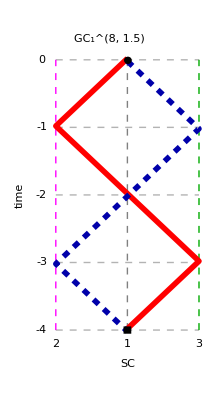
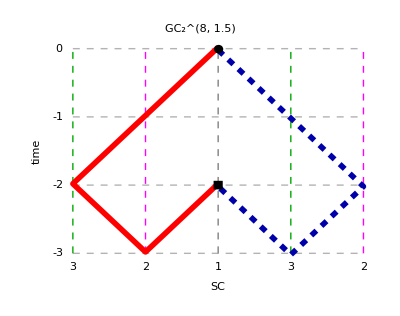
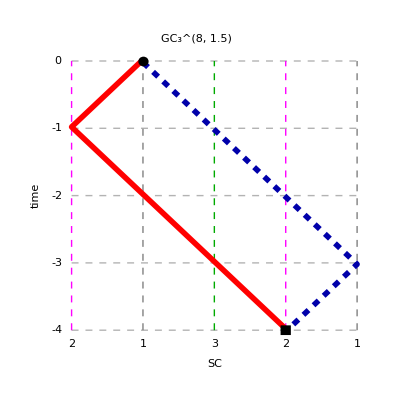
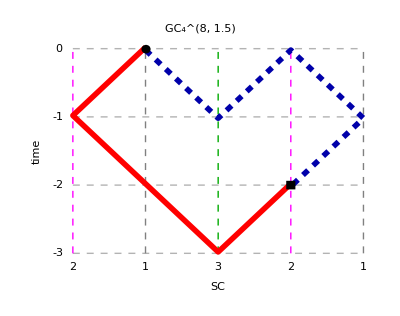

```mathematica
n1=8;
Table[spaceTimePlot2[data[n1,"m1g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,1.5,i1}]],{i1,4}]
```

Calculate and view the information of TDI combination

```mathematica
n1=8;
i1=1;
spaceTimePlot2[data[n1,"m1g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,1.5,i1}]]
informationTDI@data[n1,"m1g-TDI"][[i1]]
```

-Graphics-

Laser link trajectory:   1←2←1←3←1→2→1→3→1

Coordinate format:   {{{0,0},{1,-1},{0,-2},{-1,-3},{0,-4}},{{0,0},{-1,-1},{0,-2},{1,-3},{0,-4}}}

Defining formula (two virtual optical paths):   {η_1+𝒟_(33') η_(1')+𝒟_3 η_(2')+𝒟_(33'2') η_3,𝒟_(2'2) η_1+η_(1')+𝒟_(2'23) η_(2')+𝒟_(2') η_3}

Defining formula:   -((-1+𝒟_(2'2)) η_1)+(-1+𝒟_(33')) η_(1')+(-𝒟_(2'23)+𝒟_3) η_(2')+(-𝒟_(2')+𝒟_(33'2')) η_3

Laser noise residual:   (𝒟_(33'2'2)-𝒟_(2'233'))(ṗ)_1

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,4,-4}

Evaluation index d for the modified second-generation TDI:   {0,2,-2,0,2,-2}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-m y,0,-m+m n z,-1+n z,z-m y z,0}

Polynomial vector format (3 variables x,y,z):   {1-y^2,0,-y+y z^2,-1+z^2,z-y^2 z,0}

Polynomial vector format (1 variable x):   {1-x^2,0,-x+x^3,-1+x^2,x-x^3,0}

```mathematica
n1=8;
i1=2;
spaceTimePlot2[data[n1,"m1g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,1.5,i1}]]
informationTDI@data[n1,"m1g-TDI"][[i1]]
```

-Graphics-

Laser link trajectory:   1←2←3←2→1←3→2→3→1

Coordinate format:   {{{0,0},{1,-1},{2,-2},{1,-3},{0,-2}},{{0,0},{-1,-1},{-2,-2},{-1,-3},{0,-2}}}

Defining formula (two virtual optical paths):   {η_1-𝒟_(311'OverBar[3]) η_1+𝒟_3 η_2+𝒟_31 η_(3'),η_(1')-𝒟_(2'1'1OverBar[2]') η_(1')+𝒟_(2'1') η_2+𝒟_(2') η_(3')}

Defining formula:   -((-1+𝒟_(311'OverBar[3])) η_1)+(-1+𝒟_(2'1'1OverBar[2]')) η_(1')+(-𝒟_(2'1')+𝒟_3) η_2+(-𝒟_(2')+𝒟_31) η_(3')

Laser noise residual:   (𝒟_(311'OverBar[3])-𝒟_(2'1'1OverBar[2]'))(ṗ)_1

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,2,-2}

Evaluation index d for the modified second-generation TDI:   {-1,0,-2,1,2,0}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-l x,-l m+z,0,-1+l x,0,-m+x z}

Polynomial vector format (3 variables x,y,z):   {1-x^2,-x y+z,0,-1+x^2,0,-y+x z}

Polynomial vector format (1 variable x):   {1-x^2,x-x^2,0,-1+x^2,0,-x+x^2}

```mathematica
n1=8;
i1=3;
spaceTimePlot2[data[n1,"m1g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,1.5,i1}]]
informationTDI@data[n1,"m1g-TDI"][[i1]]
```

-Graphics-

Laser link trajectory:   1←2←1←3←2→1→2→3→1

Coordinate format:   {{{0,0},{1,-1},{0,-2},{-1,-3},{-2,-4}},{{0,0},{-1,-1},{-2,-2},{-3,-3},{-2,-4}}}

Defining formula (two virtual optical paths):   {η_1+𝒟_(33') η_(1')+𝒟_3 η_(2')+𝒟_(33'2') η_(3'),𝒟_(2'1'3') η_1+η_(1')+𝒟_(2'1') η_(2')+𝒟_(2') η_(3')}

Defining formula:   -((-1+𝒟_(2'1'3')) η_1)+(-1+𝒟_(33')) η_(1')+(-𝒟_(2'1')+𝒟_3) η_(2')+(-𝒟_(2')+𝒟_(33'2')) η_(3')

Laser noise residual:   (𝒟_(33'2'1')-𝒟_(2'1'3'3))(ṗ)_2

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {2,2,-4}

Evaluation index d for the modified second-generation TDI:   {0,0,-3,2,2,-1}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-l m n,0,0,-1+n z,-l m+z,-m+m n z}

Polynomial vector format (3 variables x,y,z):   {1-x y z,0,0,-1+z^2,-x y+z,-y+y z^2}

Polynomial vector format (1 variable x):   {1-x^3,0,0,-1+x^2,x-x^2,-x+x^3}

```mathematica
n1=8;
i1=4;
spaceTimePlot2[data[n1,"m1g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,1.5,i1}]]
informationTDI@data[n1,"m1g-TDI"][[i1]]
```

-Graphics-

Laser link trajectory:   1←2←1←3→2→1→2←3→1

Coordinate format:   {{{0,0},{1,-1},{0,-2},{-1,-3},{-2,-2}},{{0,0},{-1,-1},{-2,0},{-3,-1},{-2,-2}}}

Defining formula (two virtual optical paths):   {η_1+𝒟_(33') η_(1')-𝒟_(33'2'OverBar[1]) η_2+𝒟_3 η_(2'),𝒟_(2'OverBar[1]3') η_1+η_(1')-𝒟_(2'OverBar[1]) η_2+𝒟_(2'OverBar[1]) η_(2')}

Defining formula:   -((-1+𝒟_(2'OverBar[1]3')) η_1)+(-1+𝒟_(33')) η_(1')+(𝒟_(2'OverBar[1])-𝒟_(33'2'OverBar[1])) η_2+(-𝒟_(2'OverBar[1])+𝒟_3) η_(2')

Laser noise residual:   (𝒟_(33'2'OverBar[1])-𝒟_(2'OverBar[1]3'3))(ṗ)_2

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {-2,2,0}

Evaluation index d for the modified second-generation TDI:   {-2,0,-1,0,2,1}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-(m n)/x,m/x-(m n z)/x,0,-1+n z,-m/x+z,0}

Polynomial vector format (3 variables x,y,z):   {1-(y z)/x,y/x-(y z^2)/x,0,-1+z^2,-y/x+z,0}

Polynomial vector format (1 variable x):   {1-x,1-x^2,0,-1+x^2,-1+x,0}

Plot sensitivity curves

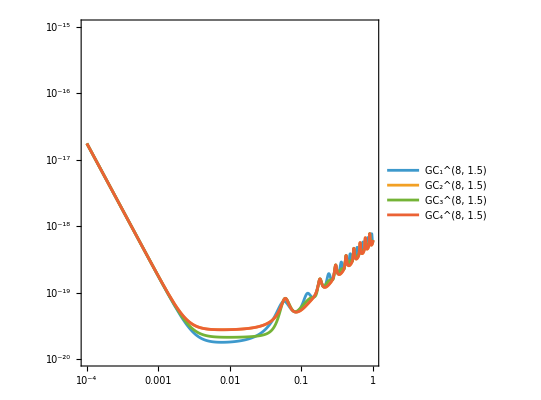

```mathematica
sensitivityFunctionPlot["path"][data[n1,"m1g-TDI"],PlotLegends->Table[labelFromIndex[{n1,1.5,i}],{i,4}]]
```

### 10-Link

Import data from the combination library

```mathematica
data[10,"m1g-TDI"]=Import[NotebookDirectory[]<>"data\\10-m1g-TDI.txt","Lines"];
Length@%
```

2

Plot spacetime diagrams of some TDI combination

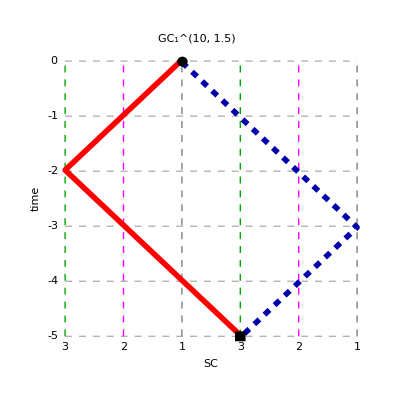
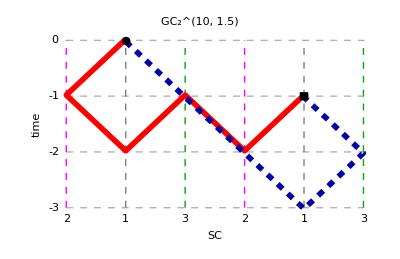

```mathematica
n1=10;
Table[spaceTimePlot2[data[n1,"m1g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,1.5,i1}]],{i1,2}]
```

Calculate and view the information of a TDI combination

```mathematica
n1=10;
i1=1;
spaceTimePlot2[data[n1,"m1g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,1.5,i1}]]
informationTDI@data[n1,"m1g-TDI"][[i1]]
```

-Graphics-

Laser link trajectory:   1←2←3←2←1←3→2→1→2→3→1

Coordinate format:   {{{0,0},{1,-1},{2,-2},{1,-3},{0,-4},{-1,-5}},{{0,0},{-1,-1},{-2,-2},{-3,-3},{-2,-4},{-1,-5}}}

Defining formula (two virtual optical paths):   {η_1+𝒟_(311'3') η_(1')+𝒟_3 η_2+𝒟_(311') η_(2')+𝒟_31 η_(3'),𝒟_(2'1'3') η_1+η_(1')+𝒟_(2'1'3'3) η_2+𝒟_(2'1') η_(2')+𝒟_(2') η_(3')}

Defining formula:   -((-1+𝒟_(2'1'3')) η_1)+(-1+𝒟_(311'3')) η_(1')+(-𝒟_(2'1'3'3)+𝒟_3) η_2+(-𝒟_(2'1')+𝒟_(311')) η_(2')+(-𝒟_(2')+𝒟_31) η_(3')

Laser noise residual:   (𝒟_(311'3'2')-𝒟_(2'1'3'31))(ṗ)_3

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {-2,4,-2}

Evaluation index d for the modified second-generation TDI:   {-3,0,-3,1,4,1}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-l m n,z-l m n z,0,-1+l n x z,-l m+l x z,-m+x z}

Polynomial vector format (3 variables x,y,z):   {1-x y z,z-x y z^2,0,-1+x^2 z^2,-x y+x^2 z,-y+x z}

Polynomial vector format (1 variable x):   {1-x^3,x-x^4,0,-1+x^4,-x^2+x^3,-x+x^2}

Plot sensitivity curve

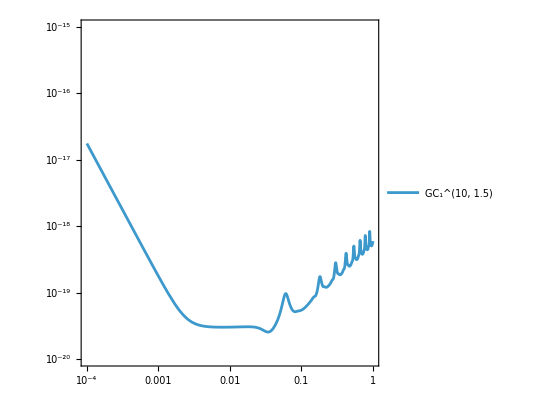

```mathematica
sensitivityFunctionPlot["path"][data[n1,"m1g-TDI"][[i1]],PlotLegends->{labelFromIndex[{n1,1.5,i1}]}]
```

### 12-Link

Import data from the combination library

```mathematica
data[12,"2g-TDI"]=Import[NotebookDirectory[]<>"data\\12-2g-TDI.txt","Lines"];
Length@%
```

3

Plot spacetime diagrams of some TDI combination

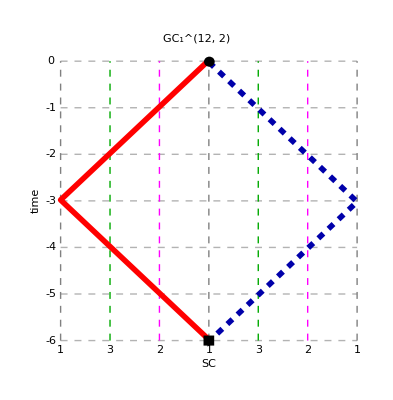
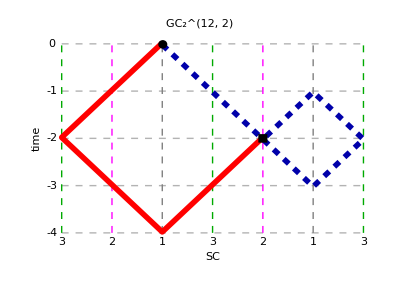
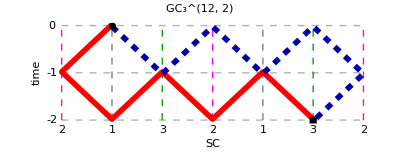

```mathematica
n1=12;
Table[spaceTimePlot2[data[n1,"2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2,i1}]],{i1,3}]
```

Calculate and view the information of TDI combination

```mathematica
n1=12;
i1=1;
spaceTimePlot2[data[n1,"2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2,i1}]]
informationTDI@data[n1,"2g-TDI"][[i1]]
```

-Graphics-

Laser link trajectory:   1←2←3←1←3←2←1→3→2→1→2→3→1

Coordinate format:   {{{0,0},{1,-1},{2,-2},{3,-3},{2,-4},{1,-5},{0,-6}},{{0,0},{-1,-1},{-2,-2},{-3,-3},{-2,-4},{-1,-5},{0,-6}}}

Defining formula (two virtual optical paths):   {η_1+𝒟_312 η_(1')+𝒟_3 η_2+𝒟_(3122'1') η_(2')+𝒟_31 η_3+𝒟_(3122') η_(3'),𝒟_(2'1'3') η_1+η_(1')+𝒟_(2'1'3'3) η_2+𝒟_(2'1') η_(2')+𝒟_(2'1'3'31) η_3+𝒟_(2') η_(3')}

Defining formula:   -((-1+𝒟_(2'1'3')) η_1)+(-1+𝒟_312) η_(1')+(-𝒟_(2'1'3'3)+𝒟_3) η_2+(-𝒟_(2'1')+𝒟_(3122'1')) η_(2')+(-𝒟_(2'1'3'31)+𝒟_31) η_3+(-𝒟_(2')+𝒟_(3122')) η_(3')

Laser noise residual:   (𝒟_(3122'1'3')-𝒟_(2'1'3'312))(ṗ)_1

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,0,0}

Evaluation index d for the modified second-generation TDI:   {-3,-3,-3,3,3,3}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-l m n,z-l m n z,x z-l m n x z,-1+x y z,-l m+l m x y z,-m+m x y z}

Polynomial vector format (3 variables x,y,z):   {1-x y z,z-x y z^2,x z-x^2 y z^2,-1+x y z,-x y+x^2 y^2 z,-y+x y^2 z}

Polynomial vector format (1 variable x):   {1-x^3,x-x^4,x^2-x^5,-1+x^3,-x^2+x^5,-x+x^4}

Plot sensitivity curve

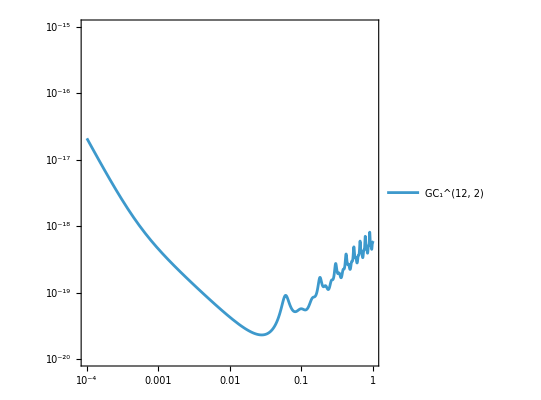

```mathematica
sensitivityFunctionPlot["path"][data[n1,"2g-TDI"][[i1]],PlotLegends->{labelFromIndex[{n1,2,i1}]}]
```

### 14-Link

Import data from the combination library

```mathematica
data[14,"2g-TDI"]=Import[NotebookDirectory[]<>"data\\14-2g-TDI.txt","Lines"];
Length@%
```

4

Plot spacetime diagrams of some TDI combination

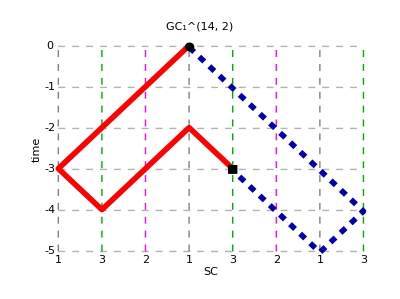
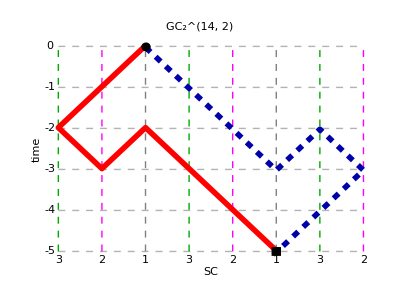
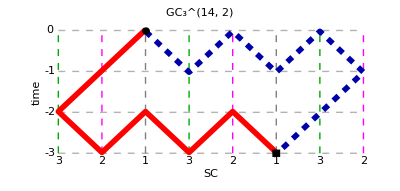
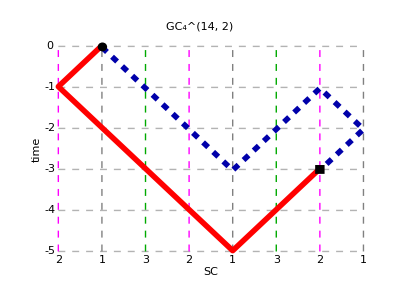

```mathematica
n1=14;
Table[spaceTimePlot2[data[n1,"2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2,i1}]],{i1,4}]
```

Calculate and view the information of a TDI combination

```mathematica
n1=14;
i1=2;
spaceTimePlot2[data[n1,"2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2,i1}]]
informationTDI@data[n1,"2g-TDI"][[i1]]
```

-Graphics-

Laser link trajectory:   1←2←3←2→1←3←2←1→3→2→3←1→2→3→1

Coordinate format:   {{{0,0},{1,-1},{2,-2},{1,-3},{0,-2},{-1,-3},{-2,-4},{-3,-5}},{{0,0},{-1,-1},{-2,-2},{-3,-3},{-4,-2},{-5,-3},{-4,-4},{-3,-5}}}

Defining formula (two virtual optical paths):   {η_1-𝒟_(311'OverBar[3]) η_1+𝒟_(311'OverBar[3]) η_(1')+𝒟_3 η_2+𝒟_(311'OverBar[3]2'1') η_(2')+𝒟_31 η_(3')+𝒟_(311'OverBar[3]2') η_(3'),η_(1')+𝒟_(2'1'3'OverBar[2]1') η_2+𝒟_(2'1') η_(2')-𝒟_(2'1'3'OverBar[2]) η_3+𝒟_(2'1'3'OverBar[2]1'1) η_3+𝒟_(2') η_(3')+𝒟_(2'1'3'OverBar[2]) η_(3')}

Defining formula:   -((-1+𝒟_(311'OverBar[3])) η_1)+(-1+𝒟_(311'OverBar[3])) η_(1')+(-𝒟_(2'1'3'OverBar[2]1')+𝒟_3) η_2+(-𝒟_(2'1')+𝒟_(311'OverBar[3]2'1')) η_(2')+(𝒟_(2'1'3'OverBar[2])-𝒟_(2'1'3'OverBar[2]1'1)) η_3+(-𝒟_(2')-𝒟_(2'1'3'OverBar[2])+𝒟_31+𝒟_(311'OverBar[3]2')) η_(3')

Laser noise residual:   (𝒟_(311'OverBar[3]2'1'3')-𝒟_(2'1'3'OverBar[2]1'12))(ṗ)_1

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,0,0}

Evaluation index d for the modified second-generation TDI:   {-2,-2,-2,2,2,2}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-l x,-(l^2 m n)/y+z,(l m n)/y-(l^2 m n x)/y,-1+l x,-l m+l^2 m x,-m+l m x-(l m n)/y+x z}

Polynomial vector format (3 variables x,y,z):   {1-x^2,z-x^2 z,x z-x^3 z,-1+x^2,-x y+x^3 y,-y+x^2 y}

Polynomial vector format (1 variable x):   {1-x^2,x-x^3,x^2-x^4,-1+x^2,-x^2+x^4,-x+x^3}

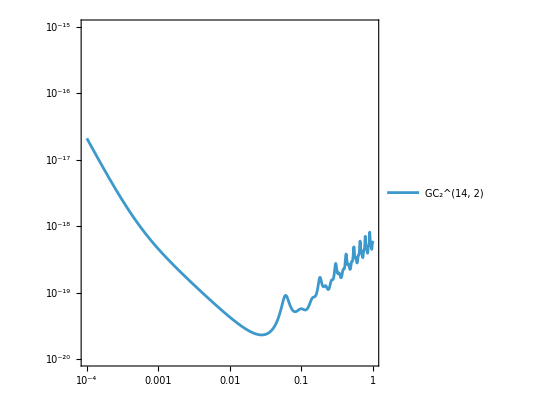

```mathematica
sensitivityFunctionPlot["path"][data[n1,"2g-TDI"][[i1]],PlotLegends->{labelFromIndex[{n1,2,i1}]}]
```

### 16-Link

Import data from the combination library

```mathematica
data[16,"m2g-TDI"]=Import[NotebookDirectory[]<>"data\\16-m2g-TDI.txt","Lines"];
Length@%
```

9

Plot spacetime diagrams of some TDI combination

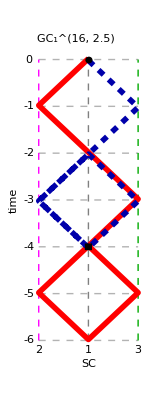
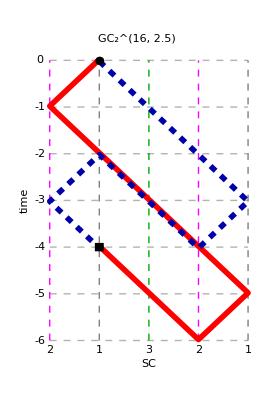
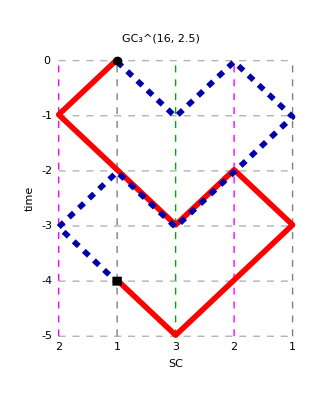
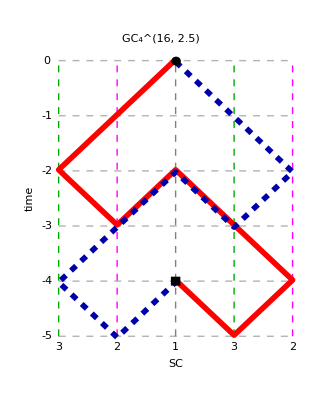
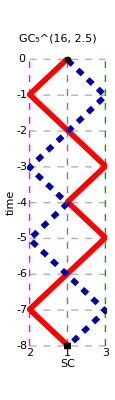
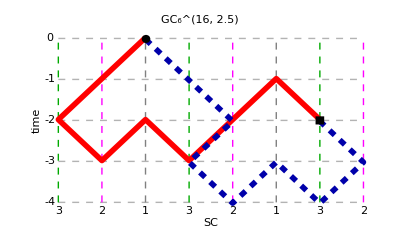
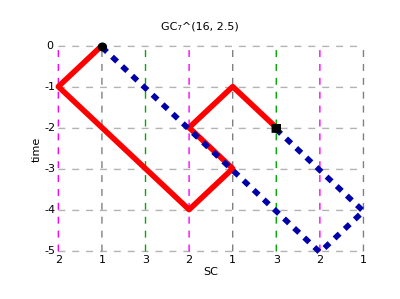
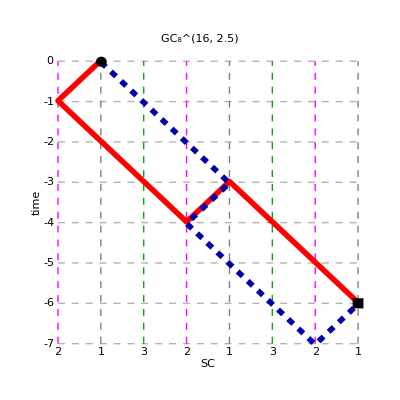

```mathematica
n1=16;
Table[spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->Style[markFromIndex[{n1,2.5,i1}],Black,FontFamily->"Times",FontSize->14]],{i1,9}]
```

Calculate and view the information of a TDI combination

```mathematica
n1=16;
i1=3;
spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]]
informationTDI@data[n1,"m2g-TDI"][[i1]]
```

-Graphics-

Laser link trajectory:   1←2←1←3→2←1←2←3→1→2→1←3→2→1→2←3→1

Coordinate format:   {{{0,0},{1,-1},{0,-2},{-1,-3},{-2,-2},{-3,-3},{-2,-4},{-1,-5},{0,-4}},{{0,0},{-1,-1},{-2,0},{-3,-1},{-2,-2},{-1,-3},{0,-2},{1,-3},{0,-4}}}

Defining formula (two virtual optical paths):   {η_1+𝒟_(33'2'OverBar[1]3') η_1+𝒟_(33') η_(1')-𝒟_(33'2'OverBar[1]3'31OverBar[2]') η_(1')-𝒟_(33'2'OverBar[1]) η_2+𝒟_(33'2'OverBar[1]3'3) η_2+𝒟_3 η_(2')+𝒟_(33'2'OverBar[1]) η_(2'),𝒟_(2'OverBar[1]3') η_1+𝒟_(2'OverBar[1]3'31OverBar[2]') η_1+η_(1')-𝒟_(2'OverBar[1]3'31OverBar[2]') η_(1')-𝒟_(2'OverBar[1]) η_2+𝒟_(2'OverBar[1]3'3) η_2+𝒟_(2'OverBar[1]) η_(2')+𝒟_(2'OverBar[1]3'31OverBar[2]'3) η_(2')}

Defining formula:   -((-1+𝒟_(2'OverBar[1]3')+𝒟_(2'OverBar[1]3'31OverBar[2]')-𝒟_(33'2'OverBar[1]3')) η_1)+(-1+𝒟_(2'OverBar[1]3'31OverBar[2]')+𝒟_(33')-𝒟_(33'2'OverBar[1]3'31OverBar[2]')) η_(1')+(𝒟_(2'OverBar[1])-𝒟_(2'OverBar[1]3'3)-𝒟_(33'2'OverBar[1])+𝒟_(33'2'OverBar[1]3'3)) η_2+(-𝒟_(2'OverBar[1])-𝒟_(2'OverBar[1]3'31OverBar[2]'3)+𝒟_3+𝒟_(33'2'OverBar[1])) η_(2')

Laser noise residual:   (𝒟_(33'2'OverBar[1]3'31OverBar[2]')-𝒟_(2'OverBar[1]3'31OverBar[2]'33'))(ṗ)_1

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,0,0}

Evaluation index d for the modified second-generation TDI:   {0,0,0,0,0,0}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-(m n)/x-n z+(m n^2 z)/x,m/x-(2 m n z)/x+(m n^2 z^2)/x,0,-1+2 n z-n^2 z^2,-m/x+z+(m n z)/x-n z^2,0}

Polynomial vector format (3 variables x,y,z):   {1-(y z)/x-z^2+(y z^3)/x,y/x-(2 y z^2)/x+(y z^4)/x,0,-1+2 z^2-z^4,-y/x+z+(y z^2)/x-z^3,0}

Polynomial vector format (1 variable x):   {1-x-x^2+x^3,1-2 x^2+x^4,0,-1+2 x^2-x^4,-1+x+x^2-x^3,0}

Plot sensitivity curve

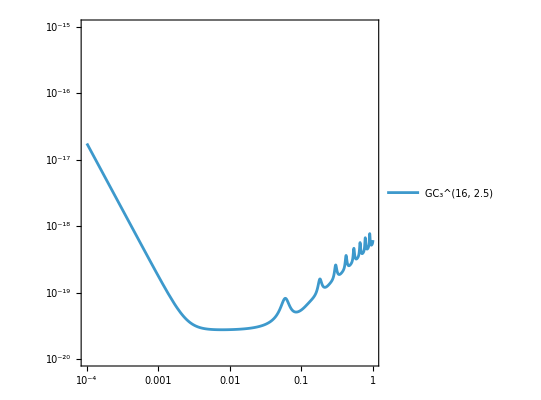

```mathematica
sensitivityFunctionPlot["path"][data[n1,"m2g-TDI"][[i1]],PlotLegends->{labelFromIndex[{n1,2.5,i1}]}]
```

The second-generation TDI combinations with 16-link has 11 different sensitivity curves

```mathematica
data[16,"2g-TDI-SF"]=laserLinkTrajectoryToPath2/@Import[NotebookDirectory[]<>"data\\16-2g-TDI-SF.txt","Lines"];
```

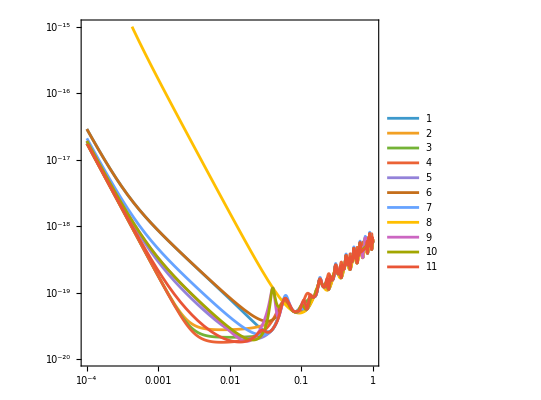

```mathematica
sensitivityFunctionPlot["path"][data[16,"2g-TDI-SF"],PlotLegends->Range[11]]
```

### 18-Link

Import data from the combination library

```mathematica
data[18,"m2g-TDI"]=Import[NotebookDirectory[]<>"data\\18-m2g-TDI.txt","Lines"];
Length@%
```

34

Plot spacetime diagrams of some TDI combination

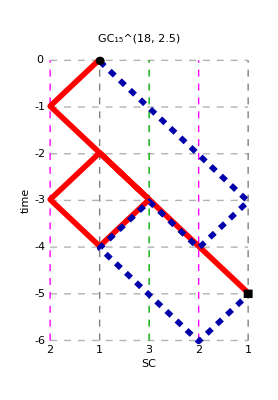
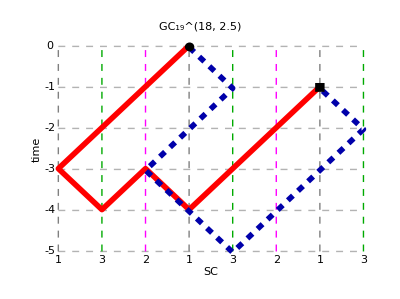
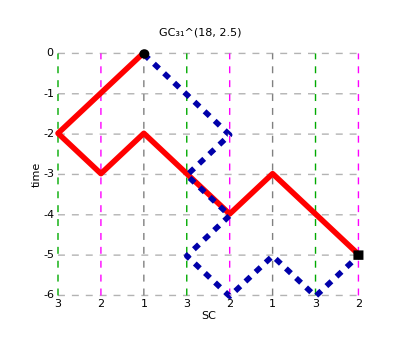
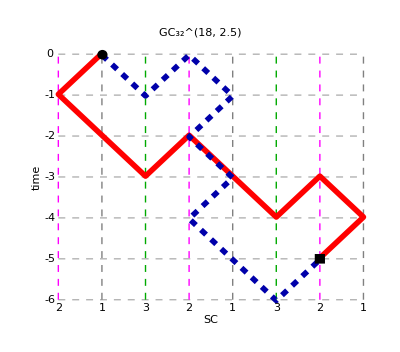
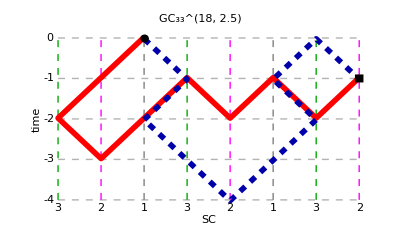

```mathematica
n1=18;
Table[spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]],{i1,Sort@RandomInteger[34,5]}]
```

Calculate and view the information of a TDI combination

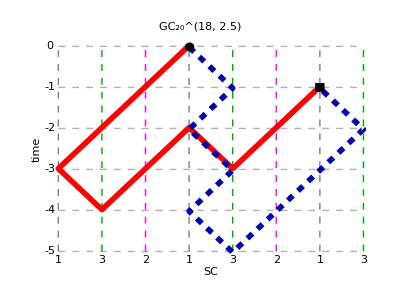

Laser link trajectory:   1←2←3←1←3→2→1←3→2→1←3←1←2←3→1→3→1→3→1

Coordinate format:   {{{0,0},{1,-1},{2,-2},{3,-3},{2,-4},{1,-3},{0,-2},{-1,-3},{-2,-2},{-3,-1}},{{0,0},{-1,-1},{0,-2},{-1,-3},{0,-4},{-1,-5},{-2,-4},{-3,-3},{-4,-2},{-3,-1}}}

Defining formula (two virtual optical paths):   {η_1-𝒟_(3122'OverBar[1]OverBar[3]) η_1-𝒟_(3122'OverBar[1]OverBar[3]2'OverBar[1]OverBar[3]) η_1+𝒟_312 η_(1')+𝒟_(3122'OverBar[1]OverBar[3]) η_(1')+𝒟_3 η_2-𝒟_(3122'OverBar[1]) η_2-𝒟_(3122'OverBar[1]OverBar[3]2'OverBar[1]) η_2+𝒟_31 η_3,-𝒟_(2'22'22'OverBar[1]OverBar[3]) η_1+η_(1')+𝒟_(2'2) η_(1')+𝒟_(2'22'2) η_(1')-𝒟_(2'22'22'OverBar[1]OverBar[3]OverBar[2]OverBar[2]') η_(1')-𝒟_(2'22'22'OverBar[1]) η_2+𝒟_(2') η_3+𝒟_(2'22') η_3-𝒟_(2'22'22'OverBar[1]OverBar[3]OverBar[2]) η_3}

Defining formula:   (1+𝒟_(2'22'22'OverBar[1]OverBar[3])-𝒟_(3122'OverBar[1]OverBar[3])-𝒟_(3122'OverBar[1]OverBar[3]2'OverBar[1]OverBar[3])) η_1+(-1-𝒟_(2'2)-𝒟_(2'22'2)+𝒟_(2'22'22'OverBar[1]OverBar[3]OverBar[2]OverBar[2]')+𝒟_312+𝒟_(3122'OverBar[1]OverBar[3])) η_(1')+(𝒟_(2'22'22'OverBar[1])+𝒟_3-𝒟_(3122'OverBar[1])-𝒟_(3122'OverBar[1]OverBar[3]2'OverBar[1])) η_2+(-𝒟_(2')-𝒟_(2'22')+𝒟_(2'22'22'OverBar[1]OverBar[3]OverBar[2])+𝒟_31) η_3

Laser noise residual:   (𝒟_(3122'OverBar[1]OverBar[3]2'OverBar[1]OverBar[3])-𝒟_(2'22'22'OverBar[1]OverBar[3]OverBar[2]OverBar[2]'))(ṗ)_1

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,0,0}

Evaluation index d for the modified second-generation TDI:   {0,0,0,0,0,0}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-m y-(m^2 y)/(x z)+(m^3 y^2)/(x z),-(m^2 y)/x+(m^3 y^2)/x+z-m y z,-m-m^2 y+(m^3 y)/(x z)+x z,-1-m^2 y^2+(m^2 y)/(x z)+x y z,0,0}

Polynomial vector format (3 variables x,y,z):   {1-y^2-y^3/(x z)+y^5/(x z),-y^3/x+y^5/x+z-y^2 z,-y-y^3+y^4/(x z)+x z,-1-y^4+y^3/(x z)+x y z,0,0}

Polynomial vector format (1 variable x):   {1-x-x^2+x^3,x-x^2-x^3+x^4,-x+2 x^2-x^3,-1+x+x^3-x^4,0,0}

```mathematica
n1=18;
i1=20;
gc[n1]=spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]]
informationTDI@data[n1,"m2g-TDI"][[i1]]
```

Plot sensitivity curve

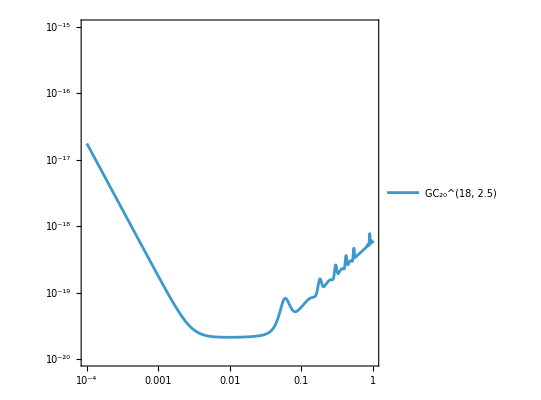

```mathematica
sensitivityFunctionPlot["path"][data[n1,"m2g-TDI"][[i1]],PlotLegends->{labelFromIndex[{n1,2.5,i1}]}]
```

### 20-Link

Import data from the combination library

```mathematica
data[20,"m2g-TDI"]=Import[NotebookDirectory[]<>"data\\20-m2g-TDI.txt","Lines"];
Length@%
```

185

Plot spacetime diagrams of some TDI combination

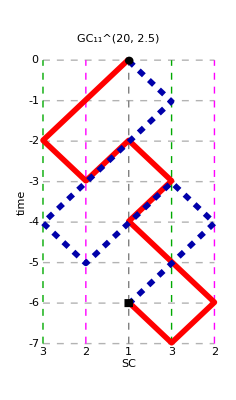
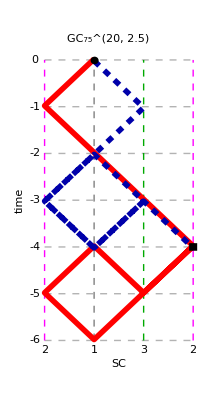
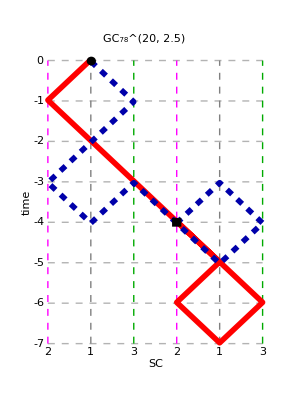
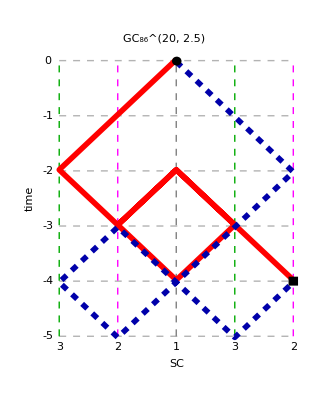
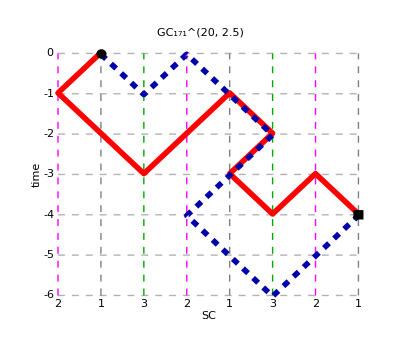

```mathematica
n1=20;
Table[spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]],{i1,Sort@RandomInteger[185,5]}]
```

Calculate and view the information of a TDI combination

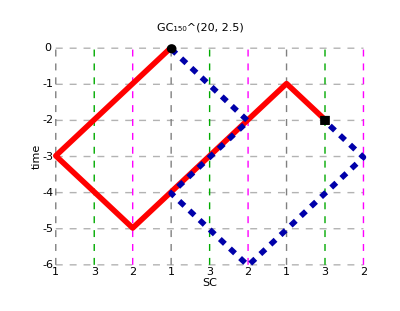

Laser link trajectory:   1←2←3←1←3←2→1→3→2→1←3←2←3←1←2→3→1→3→2→3→1

Coordinate format:   {{{0,0},{1,-1},{2,-2},{3,-3},{2,-4},{1,-5},{0,-4},{-1,-3},{-2,-2},{-3,-1},{-4,-2}},{{0,0},{-1,-1},{-2,-2},{-1,-3},{0,-4},{-1,-5},{-2,-6},{-3,-5},{-4,-4},{-5,-3},{-4,-2}}}

Defining formula (two virtual optical paths):   {η_1-𝒟_(3122'1'OverBar[3]) η_1-𝒟_(3122'1'OverBar[3]OverBar[2]OverBar[1]OverBar[3]) η_1+𝒟_312 η_(1')+𝒟_(3122'1'OverBar[3]OverBar[2]OverBar[1]OverBar[3]) η_(1')+𝒟_3 η_2-𝒟_(3122'1'OverBar[3]OverBar[2]OverBar[1]) η_2+𝒟_31 η_3-𝒟_(3122'1'OverBar[3]OverBar[2]) η_3+𝒟_(3122') η_(3'),-𝒟_(2'1'122'1'OverBar[3]) η_1+η_(1')+𝒟_(2'1'12) η_(1')+𝒟_(2'1') η_2-𝒟_(2'1'122'1'OverBar[3]OverBar[2]OverBar[1]) η_2+𝒟_(2'1'1) η_3-𝒟_(2'1'122'1'OverBar[3]OverBar[2]) η_3+𝒟_(2') η_(3')+𝒟_(2'1'122') η_(3')-𝒟_(2'1'122'1'OverBar[3]OverBar[2]OverBar[1]OverBar[1]') η_(3')}

Defining formula:   (1+𝒟_(2'1'122'1'OverBar[3])-𝒟_(3122'1'OverBar[3])-𝒟_(3122'1'OverBar[3]OverBar[2]OverBar[1]OverBar[3])) η_1+(-1-𝒟_(2'1'12)+𝒟_312+𝒟_(3122'1'OverBar[3]OverBar[2]OverBar[1]OverBar[3])) η_(1')+(-𝒟_(2'1')+𝒟_(2'1'122'1'OverBar[3]OverBar[2]OverBar[1])+𝒟_3-𝒟_(3122'1'OverBar[3]OverBar[2]OverBar[1])) η_2+(-𝒟_(2'1'1)+𝒟_(2'1'122'1'OverBar[3]OverBar[2])+𝒟_31-𝒟_(3122'1'OverBar[3]OverBar[2])) η_3+(-𝒟_(2')-𝒟_(2'1'122')+𝒟_(2'1'122'1'OverBar[3]OverBar[2]OverBar[1]OverBar[1]')+𝒟_(3122')) η_(3')

Laser noise residual:   (𝒟_(3122'1'OverBar[3]OverBar[2]OverBar[1]OverBar[3]2')-𝒟_(2'1'122'1'OverBar[3]OverBar[2]OverBar[1]OverBar[1]'))(ṗ)_3

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,0,0}

Evaluation index d for the modified second-generation TDI:   {0,0,0,0,0,0}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-l m x y-(l m)/z+(l^2 m^2 x y)/z,-2 l m+(l^2 m^2)/z+z,-2 l m x+(l^2 m^2 x)/z+x z,-1-l m x y+(l m)/z+x y z,0,-m-l m^2 x y+(l m^2)/z+m x y z}

Polynomial vector format (3 variables x,y,z):   {1-x^2 y^2-(x y)/z+(x^3 y^3)/z,-2 x y+(x^2 y^2)/z+z,-2 x^2 y+(x^3 y^2)/z+x z,-1-x^2 y^2+(x y)/z+x y z,0,-y-x^2 y^3+(x y^2)/z+x y^2 z}

Polynomial vector format (1 variable x):   {1-x-x^4+x^5,x-2 x^2+x^3,x^2-2 x^3+x^4,-1+x+x^3-x^4,0,-x+x^2+x^4-x^5}

```mathematica
n1=20;
i1=150;
gc[n1]=spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]]
informationTDI@data[n1,"m2g-TDI"][[i1]]
```

Plot sensitivity curve

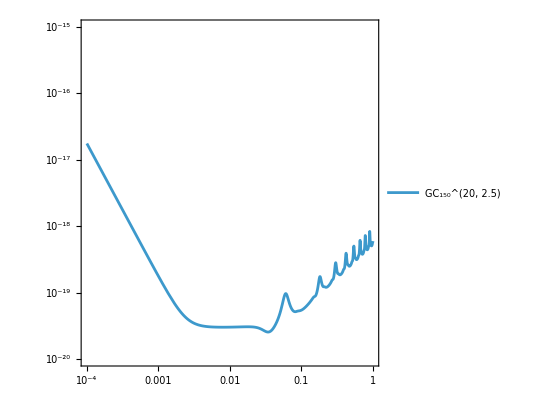

```mathematica
sensitivityFunctionPlot["path"][data[n1,"m2g-TDI"][[i1]],PlotLegends->{labelFromIndex[{n1,2.5,i1}]}]
```

### 22-Link

Import data from the combination library

```mathematica
data[22,"m2g-TDI"]=Import[NotebookDirectory[]<>"data\\22-m2g-TDI.txt","Lines"];
Length@%
```

953

Plot spacetime diagrams of some TDI combination

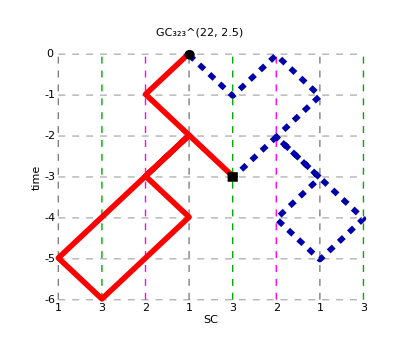
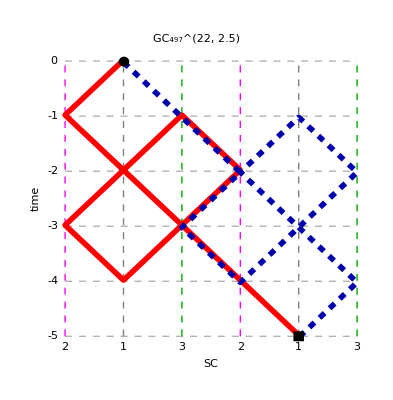
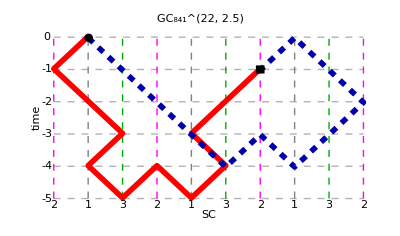
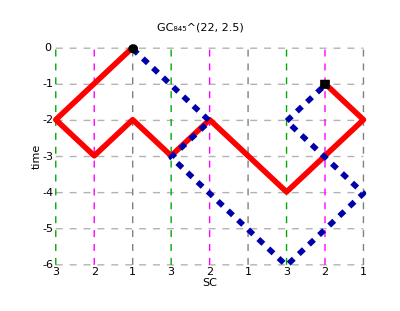
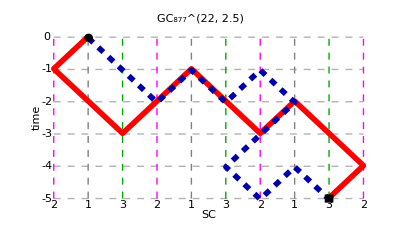

```mathematica
n1=22;
Table[spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]],{i1,Sort@RandomInteger[953,5]}]
```

Calculate and view the information of a TDI combination

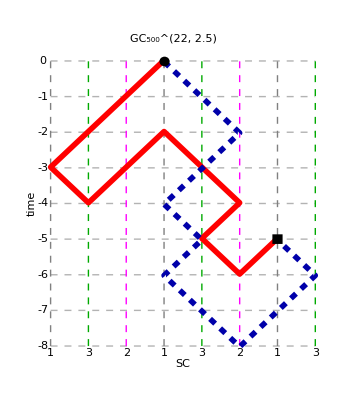

Laser link trajectory:   1←2←3←1←3→2→1←3←2←3←2→1←3←1←2→3→1→3→1→3→2→3→1

Coordinate format:   {{{0,0},{1,-1},{2,-2},{3,-3},{2,-4},{1,-3},{0,-2},{-1,-3},{-2,-4},{-1,-5},{-2,-6},{-3,-5}},{{0,0},{-1,-1},{-2,-2},{-1,-3},{0,-4},{-1,-5},{0,-6},{-1,-7},{-2,-8},{-3,-7},{-4,-6},{-3,-5}}}

Defining formula (two virtual optical paths):   {η_1-𝒟_(3122'OverBar[1]OverBar[3]) η_1-𝒟_(3122'OverBar[1]OverBar[3]2'1'11'OverBar[3]) η_1+𝒟_312 η_(1')+𝒟_(3122'OverBar[1]OverBar[3]) η_(1')+𝒟_3 η_2-𝒟_(3122'OverBar[1]) η_2+𝒟_(3122'OverBar[1]OverBar[3]2'1') η_2+𝒟_31 η_3+𝒟_(3122'OverBar[1]OverBar[3]2') η_(3')+𝒟_(3122'OverBar[1]OverBar[3]2'1'1) η_(3'),-𝒟_(2'1'122'22'1'OverBar[3]) η_1+η_(1')+𝒟_(2'1'12) η_(1')+𝒟_(2'1'122'2) η_(1')-𝒟_(2'1'122'22'1'OverBar[3]OverBar[2]OverBar[2]') η_(1')+𝒟_(2'1') η_2+𝒟_(2'1'1) η_3+𝒟_(2'1'122') η_3-𝒟_(2'1'122'22'1'OverBar[3]OverBar[2]) η_3+𝒟_(2') η_(3')+𝒟_(2'1'122'22') η_(3')}

Defining formula:   (1+𝒟_(2'1'122'22'1'OverBar[3])-𝒟_(3122'OverBar[1]OverBar[3])-𝒟_(3122'OverBar[1]OverBar[3]2'1'11'OverBar[3])) η_1+(-1-𝒟_(2'1'12)-𝒟_(2'1'122'2)+𝒟_(2'1'122'22'1'OverBar[3]OverBar[2]OverBar[2]')+𝒟_312+𝒟_(3122'OverBar[1]OverBar[3])) η_(1')+(-𝒟_(2'1')+𝒟_3-𝒟_(3122'OverBar[1])+𝒟_(3122'OverBar[1]OverBar[3]2'1')) η_2+(-𝒟_(2'1'1)-𝒟_(2'1'122')+𝒟_(2'1'122'22'1'OverBar[3]OverBar[2])+𝒟_31) η_3+(-𝒟_(2')-𝒟_(2'1'122'22')+𝒟_(3122'OverBar[1]OverBar[3]2')+𝒟_(3122'OverBar[1]OverBar[3]2'1'1)) η_(3')

Laser noise residual:   (𝒟_(3122'OverBar[1]OverBar[3]2'1'11'OverBar[3])-𝒟_(2'1'122'22'1'OverBar[3]OverBar[2]OverBar[2]'))(ṗ)_1

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,0,0}

Evaluation index d for the modified second-generation TDI:   {0,0,0,0,0,0}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-m y-(l^2 m^2 x y)/z+(l^2 m^3 x y^2)/z,-l m+l m^2 y+z-m y z,-l m x-l m^2 x y+(l^2 m^3 x y)/z+x z,-1+m y-l m x y-l m^2 x y^2+(l^2 m^2 x y)/z+x y z,0,-m+m^2 y+l m^2 x y-l m^3 x y^2}

Polynomial vector format (3 variables x,y,z):   {1-y^2-(x^3 y^3)/z+(x^3 y^5)/z,-x y+x y^3+z-y^2 z,-x^2 y-x^2 y^3+(x^3 y^4)/z+x z,-1+y^2-x^2 y^2-x^2 y^4+(x^3 y^3)/z+x y z,0,-y+y^3+x^2 y^3-x^2 y^5}

Polynomial vector format (1 variable x):   {1-x^2-x^5+x^7,x-x^2-x^3+x^4,x^2-x^3-x^5+x^6,-1+x^2+x^3-x^4+x^5-x^6,0,-x+x^3+x^5-x^7}

```mathematica
n1=22;
i1=500;
gc[n1]=spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]]
informationTDI@data[n1,"m2g-TDI"][[i1]]
```

Plot sensitivity curve

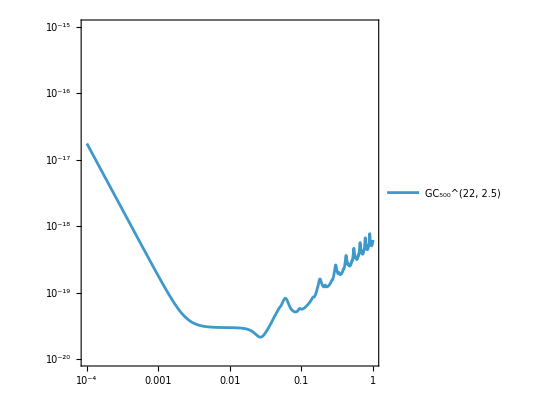

```mathematica
sensitivityFunctionPlot["path"][data[n1,"m2g-TDI"][[i1]],PlotLegends->{labelFromIndex[{n1,2.5,i1}]}]
```

### 24-Link

Import data from the combination library

```mathematica
data[24,"m2g-TDI"]=Import[NotebookDirectory[]<>"data\\24-m2g-TDI.txt","Lines"];
Length@%
```

5868

Plot spacetime diagrams of some TDI combination

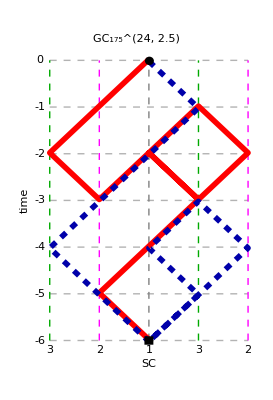
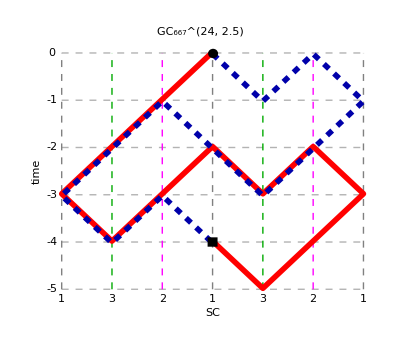
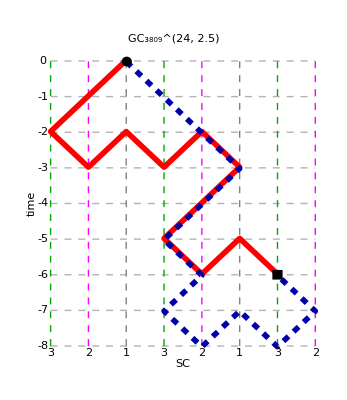
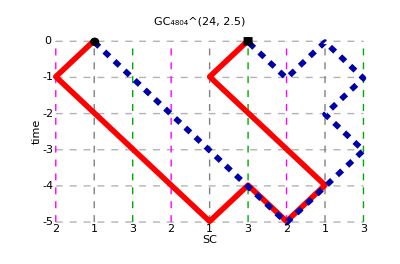
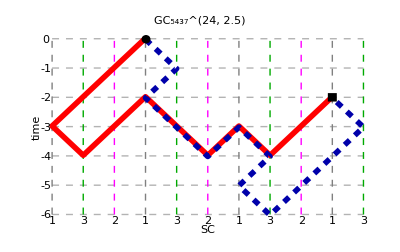

```mathematica
n1=24;
Table[spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]],{i1,Sort@RandomInteger[5868,5]}]
```

Calculate and view the information of a TDI combination

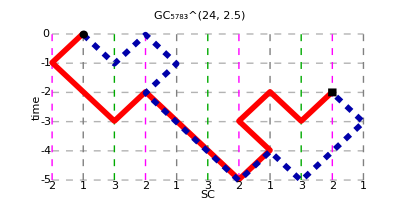

Laser link trajectory:   1←2←1←3→2←1←3←2→1→2→1←3→2←1←2←3→1←2→3→1→2→1→2←3→1

Coordinate format:   {{{0,0},{1,-1},{0,-2},{-1,-3},{-2,-2},{-3,-3},{-4,-4},{-5,-5},{-6,-4},{-5,-3},{-6,-2},{-7,-3},{-8,-2}},{{0,0},{-1,-1},{-2,0},{-3,-1},{-2,-2},{-3,-3},{-4,-4},{-5,-5},{-6,-4},{-7,-5},{-8,-4},{-9,-3},{-8,-2}}}

Defining formula (two virtual optical paths):   {η_1-𝒟_(33'2'OverBar[1]3'2'1'OverBar[3]) η_1-𝒟_(33'2'OverBar[1]3'2'1'OverBar[3]OverBar[3]'OverBar[3]) η_1+𝒟_(33') η_(1')+𝒟_(33'2'OverBar[1]3') η_(1')+𝒟_(33'2'OverBar[1]3'2'1'OverBar[3]OverBar[3]'OverBar[3]) η_(1')-𝒟_(33'2'OverBar[1]) η_2-𝒟_(33'2'OverBar[1]3'2'1'OverBar[3]OverBar[3]'OverBar[3]2'OverBar[1]) η_2+𝒟_3 η_(2')+𝒟_(33'2'OverBar[1]) η_(2')-𝒟_(33'2'OverBar[1]3'2'1'OverBar[3]OverBar[3]') η_(2')+𝒟_(33'2'OverBar[1]3'2') η_(3'),𝒟_(2'OverBar[1]3') η_1-𝒟_(2'OverBar[1]3'33'2'1'OverBar[3]) η_1-𝒟_(2'OverBar[1]3'33'2'1'OverBar[3]2'OverBar[1]OverBar[3]) η_1+η_(1')+𝒟_(2'OverBar[1]3'33') η_(1')+𝒟_(2'OverBar[1]3'33'2'1'OverBar[3]) η_(1')-𝒟_(2'OverBar[1]) η_2-𝒟_(2'OverBar[1]3'33'2'1'OverBar[3]2'OverBar[1]) η_2+𝒟_(2'OverBar[1]) η_(2')+𝒟_(2'OverBar[1]3'3) η_(2')-𝒟_(2'OverBar[1]3'33'2'1'OverBar[3]2'OverBar[1]OverBar[3]OverBar[3]') η_(2')+𝒟_(2'OverBar[1]3'33'2') η_(3')}

Defining formula:   -((-1+𝒟_(2'OverBar[1]3')-𝒟_(2'OverBar[1]3'33'2'1'OverBar[3])-𝒟_(2'OverBar[1]3'33'2'1'OverBar[3]2'OverBar[1]OverBar[3])+𝒟_(33'2'OverBar[1]3'2'1'OverBar[3])+𝒟_(33'2'OverBar[1]3'2'1'OverBar[3]OverBar[3]'OverBar[3])) η_1)+(-1-𝒟_(2'OverBar[1]3'33')-𝒟_(2'OverBar[1]3'33'2'1'OverBar[3])+𝒟_(33')+𝒟_(33'2'OverBar[1]3')+𝒟_(33'2'OverBar[1]3'2'1'OverBar[3]OverBar[3]'OverBar[3])) η_(1')+(𝒟_(2'OverBar[1])+𝒟_(2'OverBar[1]3'33'2'1'OverBar[3]2'OverBar[1])-𝒟_(33'2'OverBar[1])-𝒟_(33'2'OverBar[1]3'2'1'OverBar[3]OverBar[3]'OverBar[3]2'OverBar[1])) η_2+(-𝒟_(2'OverBar[1])-𝒟_(2'OverBar[1]3'3)+𝒟_(2'OverBar[1]3'33'2'1'OverBar[3]2'OverBar[1]OverBar[3]OverBar[3]')+𝒟_3+𝒟_(33'2'OverBar[1])-𝒟_(33'2'OverBar[1]3'2'1'OverBar[3]OverBar[3]')) η_(2')+(-𝒟_(2'OverBar[1]3'33'2')+𝒟_(33'2'OverBar[1]3'2')) η_(3')

Laser noise residual:   (𝒟_(33'2'OverBar[1]3'2'1'OverBar[3]OverBar[3]'OverBar[3]2'OverBar[1])-𝒟_(2'OverBar[1]3'33'2'1'OverBar[3]2'OverBar[1]OverBar[3]OverBar[3]'))(ṗ)_2

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,0,0}

Evaluation index d for the modified second-generation TDI:   {0,0,0,0,0,0}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-(m n)/x+(l m^3 n^2)/(x^2 z)-(l m^2 n)/(x z),(l m^3 n^2)/x^2+m/x-(l m^3 n)/(x^2 z)-(m n z)/x,0,-1-(l m^2 n^2)/x+(l m^2 n)/(x z)+n z,-m/x-(l m^2 n)/x+(l m^3 n)/(x^2 z)+z,0}

Polynomial vector format (3 variables x,y,z):   {1-y^2-(y z)/x+(y^3 z)/x,y/x-y^3/x-(y z^2)/x+(y^3 z^2)/x,0,-1+y^2+z^2-y^2 z^2,-y/x+y^3/x+z-y^2 z,0}

Polynomial vector format (1 variable x):   {1-x-x^2+x^3,1-2 x^2+x^4,0,-1+2 x^2-x^4,-1+x+x^2-x^3,0}

```mathematica
n1=24;
i1=5783;
gc[n1]=spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]]
informationTDI@data[n1,"m2g-TDI"][[i1]]
```

Plot sensitivity curve

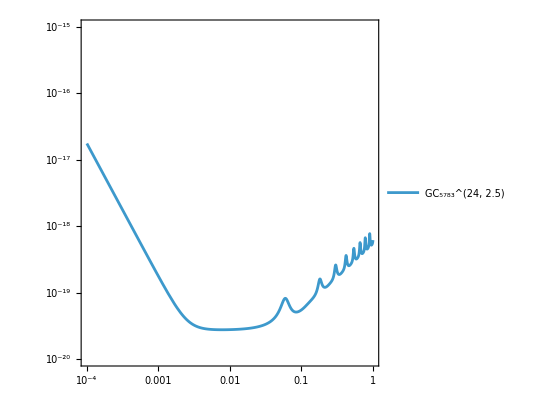

```mathematica
sensitivityFunctionPlot["path"][data[n1,"m2g-TDI"][[i1]],PlotLegends->{labelFromIndex[{n1,2.5,i1}]}]
```

### 26-Link

Import data from the combination library

```mathematica
data[26,"m2g-TDI"]=Import[NotebookDirectory[]<>"data\\26-m2g-TDI.txt","Lines"];
Length@%
```

34942

Plot spacetime diagrams of some TDI combination

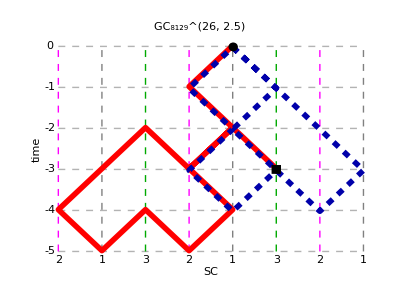
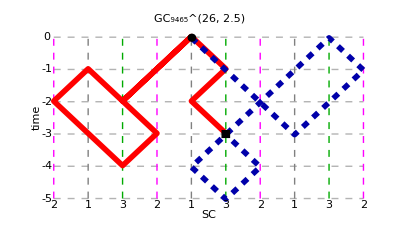
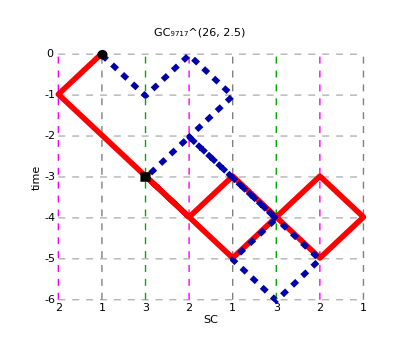
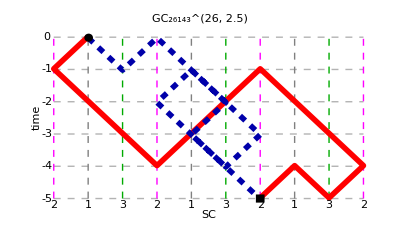
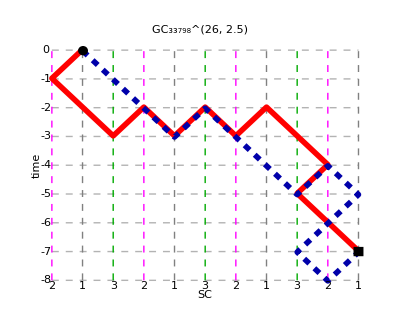

```mathematica
n1=26;
Table[spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]],{i1,Sort@RandomInteger[34942,5]}]
```

Calculate and view the information of a TDI combination

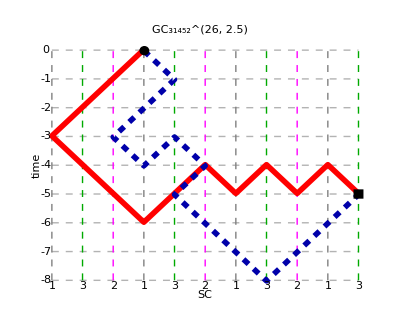

Laser link trajectory:   1←2←3←1←3←2←1→3→2←1→3←2→1←3←1←2←3→1→2→3→2→3←1→2→1→3→1

Coordinate format:   {{{0,0},{1,-1},{2,-2},{3,-3},{2,-4},{1,-5},{0,-6},{-1,-5},{-2,-4},{-3,-5},{-4,-4},{-5,-5},{-6,-4},{-7,-5}},{{0,0},{-1,-1},{0,-2},{1,-3},{0,-4},{-1,-3},{-2,-4},{-1,-5},{-2,-6},{-3,-7},{-4,-8},{-5,-7},{-6,-6},{-7,-5}}}

Defining formula (two virtual optical paths):   {η_1-𝒟_(3122'1'3'OverBar[2]OverBar[1]3'OverBar[2]1'OverBar[3]) η_1+𝒟_312 η_(1')+𝒟_(3122'1'3'OverBar[2]OverBar[1]3'OverBar[2]1'OverBar[3]) η_(1')+𝒟_3 η_2-𝒟_(3122'1'3'OverBar[2]OverBar[1]) η_2+𝒟_(3122'1') η_(2')+𝒟_(3122'1'3'OverBar[2]OverBar[1]) η_(2')+𝒟_31 η_3-𝒟_(3122'1'3'OverBar[2]) η_3-𝒟_(3122'1'3'OverBar[2]OverBar[1]3'OverBar[2]) η_3+𝒟_(3122') η_(3')+𝒟_(3122'1'3'OverBar[2]OverBar[1]3'OverBar[2]) η_(3'),𝒟_(2'2) η_1-𝒟_(2'233'OverBar[2]1'11'3'2'OverBar[1]OverBar[3]) η_1+η_(1')+𝒟_(2'233'OverBar[2]1'11'3') η_(1')+𝒟_(2'233'OverBar[2]1') η_2-𝒟_(2'233'OverBar[2]1'11'3'2'OverBar[1]) η_2+𝒟_(2'23) η_(2')+𝒟_(2'233'OverBar[2]1'11') η_(2')+𝒟_(2') η_3-𝒟_(2'233'OverBar[2]) η_3-𝒟_(2'233'OverBar[2]1'11'3'2'OverBar[1]OverBar[3]OverBar[2]) η_3+𝒟_(2'233'OverBar[2]) η_(3')+𝒟_(2'233'OverBar[2]1'1) η_(3')}

Defining formula:   -((-1+𝒟_(2'2)-𝒟_(2'233'OverBar[2]1'11'3'2'OverBar[1]OverBar[3])+𝒟_(3122'1'3'OverBar[2]OverBar[1]3'OverBar[2]1'OverBar[3])) η_1)+(-1-𝒟_(2'233'OverBar[2]1'11'3')+𝒟_312+𝒟_(3122'1'3'OverBar[2]OverBar[1]3'OverBar[2]1'OverBar[3])) η_(1')+(-𝒟_(2'233'OverBar[2]1')+𝒟_(2'233'OverBar[2]1'11'3'2'OverBar[1])+𝒟_3-𝒟_(3122'1'3'OverBar[2]OverBar[1])) η_2-(𝒟_(2'23)+𝒟_(2'233'OverBar[2]1'11')-𝒟_(3122'1')) η_(2')+𝒟_(3122'1'3'OverBar[2]OverBar[1]) η_(2')+(-𝒟_(2')+𝒟_(2'233'OverBar[2])+𝒟_(2'233'OverBar[2]1'11'3'2'OverBar[1]OverBar[3]OverBar[2])+𝒟_31-𝒟_(3122'1'3'OverBar[2])-𝒟_(3122'1'3'OverBar[2]OverBar[1]3'OverBar[2])) η_3+(-𝒟_(2'233'OverBar[2])-𝒟_(2'233'OverBar[2]1'1)+𝒟_(3122')+𝒟_(3122'1'3'OverBar[2]OverBar[1]3'OverBar[2])) η_(3')

Laser noise residual:   (𝒟_(3122'1'3'OverBar[2]OverBar[1]3'OverBar[2]1'OverBar[3]2')-𝒟_(2'233'OverBar[2]1'11'3'2'OverBar[1]OverBar[3]OverBar[2]))(ṗ)_3

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,0,0}

Evaluation index d for the modified second-generation TDI:   {0,0,0,0,0,0}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1+l^2 m^2 n^2-(l^2 m n^2)/y-m y,z-2 l m n z+l^2 m^2 n^2 z,-m+(l^2 m^2 n^2)/y+m n z+x z-l m n x z-(l m n^2 z)/y,-1+(l^2 m n^2)/y-l^2 m n^2 x z+x y z,l m n z-l^2 m n x z-m y z+l m x y z,-m n z-l m n x z+(l m n^2 z)/y+m x y z}

Polynomial vector format (3 variables x,y,z):   {1-y^2-x^2 z^2+x^2 y^2 z^2,z-2 x y z^2+x^2 y^2 z^3,-y+x z+y z^2-x z^3,-1+x y z+x^2 z^2-x^3 y z^3,-y^2 z+x^2 y^2 z+x y z^2-x^3 y z^2,x y^2 z-y z^2-x^2 y z^2+x z^3}

Polynomial vector format (1 variable x):   {1-x^2-x^4+x^6,x-2 x^4+x^7,-x+x^2+x^3-x^4,-1+x^3+x^4-x^7,-x^3+x^4+x^5-x^6,-x^3+2 x^4-x^5}

```mathematica
n1=26;
i1=31452;
gc[n1]=spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->Style[markFromIndex[{n1,2.5,i1}],Black,FontFamily->"Times",FontSize->14]]
informationTDI@data[n1,"m2g-TDI"][[i1]]
```

Plot sensitivity curve

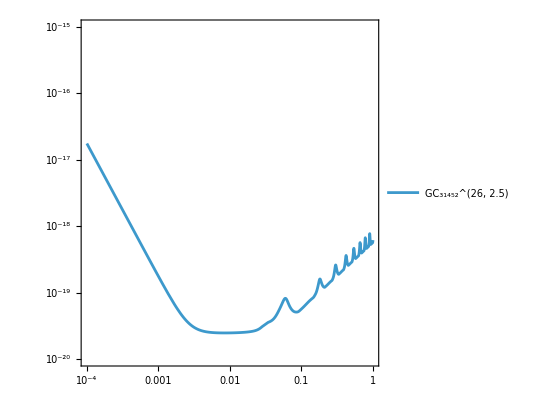

```mathematica
sensitivityFunctionPlot["path"][data[n1,"m2g-TDI"][[i1]],PlotLegends->{labelFromIndex[{n1,2.5,i1}]}]
```

### 28-Link

Import data from the combination library

```mathematica
data[28,"m2g-TDI"]=Import[NotebookDirectory[]<>"data\\28-m2g-TDI.txt","Lines"];
Length@%
```

220177

Plot spacetime diagrams of some TDI combination

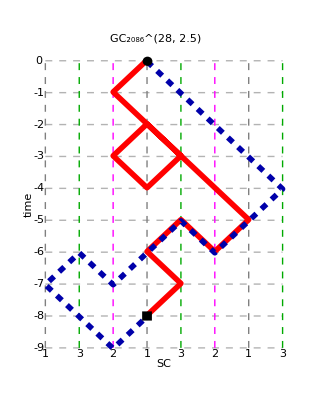
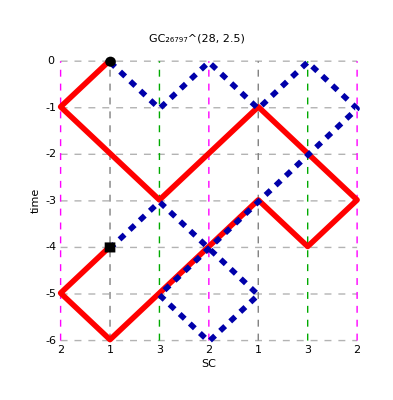
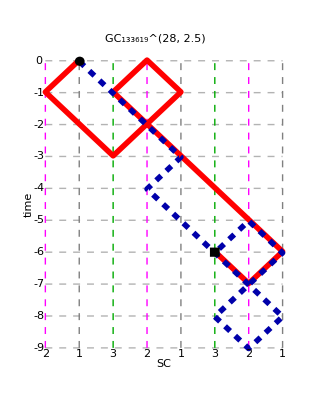
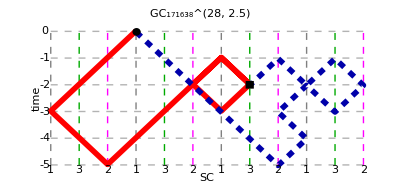
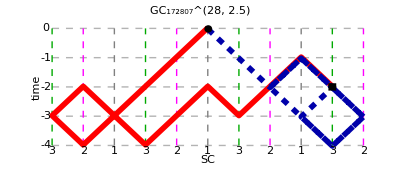

```mathematica
n1=28;Table[spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]],{i1,Sort@RandomInteger[220177,5]}]
```

Calculate and view the information of a TDI combination

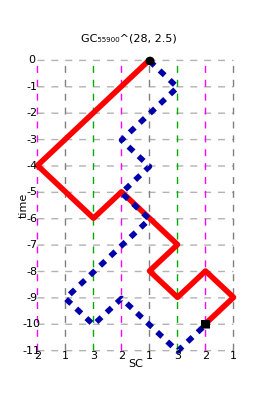

Laser link trajectory:   1←2←3←1←2←1←3→2←1←3←1←3→2←1←2←3→1→2←3→1→3→2→1→2→1→2→1→3→1

Coordinate format:   {{{0,0},{1,-1},{2,-2},{3,-3},{4,-4},{3,-5},{2,-6},{1,-5},{0,-6},{-1,-7},{0,-8},{-1,-9},{-2,-8},{-3,-9},{-2,-10}},{{0,0},{-1,-1},{0,-2},{1,-3},{0,-4},{1,-5},{0,-6},{1,-7},{2,-8},{3,-9},{2,-10},{1,-9},{0,-10},{-1,-11},{-2,-10}}}

Defining formula (two virtual optical paths):   {η_1+𝒟_312 η_1+𝒟_(31233'2'OverBar[1]3'2'22'OverBar[1]3') η_1+𝒟_(31233') η_(1')+𝒟_(31233'2'OverBar[1]3') η_(1')+𝒟_(31233'2'OverBar[1]3'2'2) η_(1')+𝒟_3 η_2-𝒟_(31233'2'OverBar[1]) η_2-𝒟_(31233'2'OverBar[1]3'2'22'OverBar[1]) η_2+𝒟_3123 η_(2')+𝒟_(31233'2'OverBar[1]) η_(2')+𝒟_(31233'2'OverBar[1]3'2'22'OverBar[1]) η_(2')+𝒟_31 η_3+𝒟_(31233'2'OverBar[1]3'2') η_3,𝒟_(2'2) η_1+𝒟_(2'233') η_1+𝒟_(2'233'33') η_1+η_(1')+𝒟_(2'233'33'312) η_(1')+𝒟_(2'233'33'3122'OverBar[1]3') η_(1')+𝒟_(2'233'33'3) η_2-𝒟_(2'233'33'3122'OverBar[1]) η_2-𝒟_(2'233'33'3122'OverBar[1]3'2'OverBar[1]) η_2+𝒟_(2'23) η_(2')+𝒟_(2'233'3) η_(2')+𝒟_(2'233'33'3122'OverBar[1]) η_(2')+𝒟_(2') η_3+𝒟_(2'233'33'31) η_3}

Defining formula:   -((-1+𝒟_(2'2)+𝒟_(2'233')+𝒟_(2'233'33')-𝒟_312-𝒟_(31233'2'OverBar[1]3'2'22'OverBar[1]3')) η_1)+(-1-𝒟_(2'233'33'312)-𝒟_(2'233'33'3122'OverBar[1]3')+𝒟_(31233')+𝒟_(31233'2'OverBar[1]3')+𝒟_(31233'2'OverBar[1]3'2'2)) η_(1')+(-𝒟_(2'233'33'3)+𝒟_(2'233'33'3122'OverBar[1])+𝒟_(2'233'33'3122'OverBar[1]3'2'OverBar[1])+𝒟_3-𝒟_(31233'2'OverBar[1])-𝒟_(31233'2'OverBar[1]3'2'22'OverBar[1])) η_2-(𝒟_(2'23)+𝒟_(2'233'3)) η_(2')+(-𝒟_(2'233'33'3122'OverBar[1])+𝒟_3123+𝒟_(31233'2'OverBar[1])+𝒟_(31233'2'OverBar[1]3'2'22'OverBar[1])) η_(2')+(-𝒟_(2')-𝒟_(2'233'33'31)+𝒟_31+𝒟_(31233'2'OverBar[1]3'2')) η_3

Laser noise residual:   (𝒟_(31233'2'OverBar[1]3'2'22'OverBar[1]3'3)-𝒟_(2'233'33'3122'OverBar[1]3'2'OverBar[1]))(ṗ)_2

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,0,0}

Evaluation index d for the modified second-generation TDI:   {0,0,0,0,0,0}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-m y-m n y z+x y z-m n^2 y z^2+(m^3 n^3 y^2 z^2)/x,z-m n y z^2-(m^3 n^2 y^2 z^2)/x-m n^2 y z^3+m^2 n^2 y^2 z^3+(m^3 n^3 y^2 z^3)/x,-m+x z+m^2 n^2 y z^2-m n^2 x y z^3,-1+m n^2 y z^2+n x y z^2+m^2 n^2 y^2 z^2-m^2 n^3 y^2 z^3-m n^2 x y^2 z^3,-m y z+x y z^2+(m^3 n^2 y^2 z^2)/x-m^2 n^2 y^2 z^3,0}

Polynomial vector format (3 variables x,y,z):   {1-y^2+x y z-y^2 z^2-y^2 z^4+(y^5 z^5)/x,z-y^2 z^3-(y^5 z^4)/x-y^2 z^5+y^4 z^5+(y^5 z^6)/x,-y+x z+y^3 z^4-x y^2 z^5,-1+x y z^3+y^2 z^4+y^4 z^4-x y^3 z^5-y^4 z^6,-y^2 z+x y z^2+(y^5 z^4)/x-y^4 z^5,0}

Polynomial vector format (1 variable x):   {1-x^2+x^3-x^4-x^6+x^9,x-x^5-x^7-x^8+x^9+x^10,-x+x^2+x^7-x^8,-1+x^5+x^6+x^8-x^9-x^10,-x^3+x^4+x^8-x^9,0}

```mathematica
n1=28;
i1=55900;
gc[n1]=spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]]
informationTDI@data[n1,"m2g-TDI"][[i1]]
```

Plot sensitivity curve

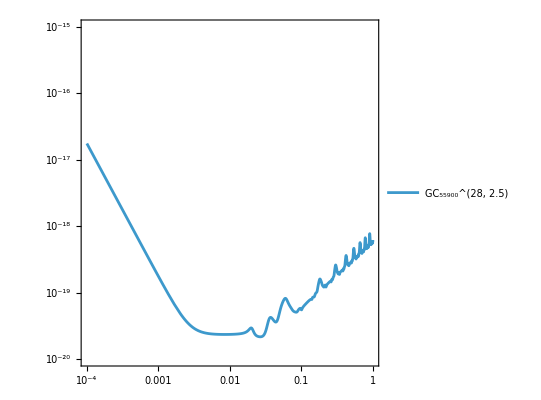

```mathematica
sensitivityFunctionPlot["path"][data[n1,"m2g-TDI"][[i1]],PlotLegends->{labelFromIndex[{n1,2.5,i1}]}]
```

### 30-Link

Import data from the combination library

```mathematica
data[30,"m2g-TDI"]=Import[NotebookDirectory[]<>"data\\30-m2g-TDI.txt","Lines"];
Length@%
```

1388693

Plot spacetime diagrams of some TDI combination

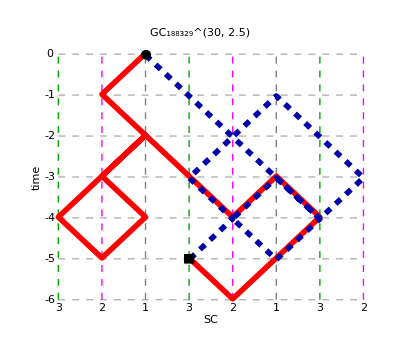
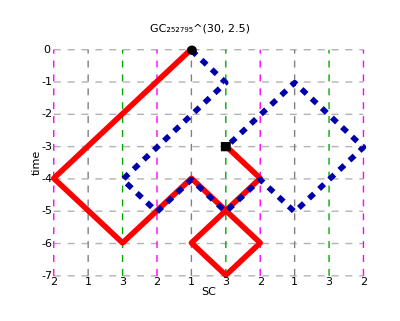
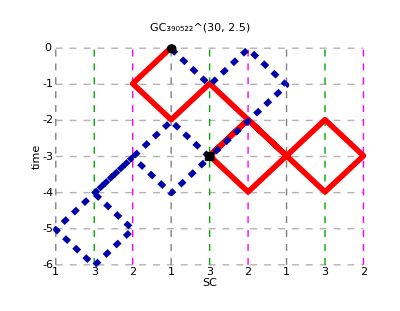
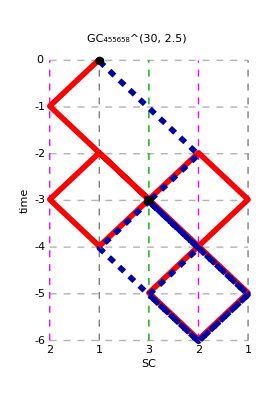
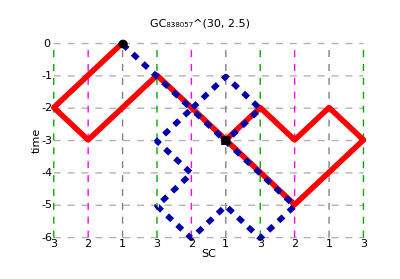

```mathematica
n1=30;
Table[spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->labelFromIndex[{n1,2.5,i1}]],{i1,Sort@RandomInteger[1388693,5]}]
```

Calculate and view the information of a TDI combination

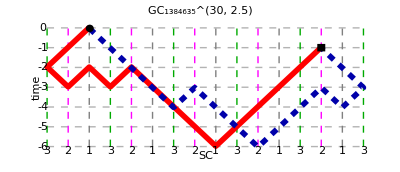

Laser link trajectory:   1←2←3←2→1←3→2←1←3←2←1→3→2→1→3→2←1←3←1→2←3←1←2→3→1→2←3→1→2→3→1

Coordinate format:   {{{0,0},{1,-1},{2,-2},{1,-3},{0,-2},{-1,-3},{-2,-2},{-3,-3},{-4,-4},{-5,-5},{-6,-6},{-7,-5},{-8,-4},{-9,-3},{-10,-2},{-11,-1}},{{0,0},{-1,-1},{-2,-2},{-3,-3},{-4,-4},{-5,-3},{-6,-4},{-7,-5},{-8,-6},{-9,-5},{-10,-4},{-11,-3},{-12,-4},{-13,-3},{-12,-2},{-11,-1}}}

Defining formula (two virtual optical paths):   {η_1-𝒟_(311'OverBar[3]) η_1-𝒟_(311'OverBar[3]2'OverBar[1]3'2'1'3'OverBar[2]OverBar[1]OverBar[3]) η_1+𝒟_(311'OverBar[3]) η_(1')+𝒟_(311'OverBar[3]2'OverBar[1]3') η_(1')+𝒟_3 η_2-𝒟_(311'OverBar[3]2'OverBar[1]) η_2-𝒟_(311'OverBar[3]2'OverBar[1]3'2'1'3'OverBar[2]OverBar[1]) η_2-𝒟_(311'OverBar[3]2'OverBar[1]3'2'1'3'OverBar[2]OverBar[1]OverBar[3]OverBar[2]OverBar[1]) η_2+𝒟_(311'OverBar[3]2'OverBar[1]) η_(2')+𝒟_(311'OverBar[3]2'OverBar[1]3'2'1') η_(2')-𝒟_(311'OverBar[3]2'OverBar[1]3'2'1'3'OverBar[2]) η_3-𝒟_(311'OverBar[3]2'OverBar[1]3'2'1'3'OverBar[2]OverBar[1]OverBar[3]OverBar[2]) η_3+𝒟_31 η_(3')+𝒟_(311'OverBar[3]2'OverBar[1]3'2') η_(3'),-𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]) η_1+η_(1')+𝒟_(2'1'3') η_(1')+𝒟_(2'1'3'2'OverBar[1]3') η_(1')-𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]OverBar[1]3'OverBar[2]OverBar[2]') η_(1')-𝒟_(2'1'3'2'OverBar[1]) η_2-𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]OverBar[1]) η_2+𝒟_(2'1') η_(2')+𝒟_(2'1'3'2'OverBar[1]) η_(2')+𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]OverBar[1]) η_(2')-𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]OverBar[1]3'OverBar[2]OverBar[2]'OverBar[3]') η_(2')-𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]) η_3-𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]OverBar[1]3'OverBar[2]) η_3+𝒟_(2') η_(3')+𝒟_(2'1'3'2'OverBar[1]3'2') η_(3')}

Defining formula:   (1+𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3])-𝒟_(311'OverBar[3])-𝒟_(311'OverBar[3]2'OverBar[1]3'2'1'3'OverBar[2]OverBar[1]OverBar[3])) η_1+(-1-𝒟_(2'1'3')-𝒟_(2'1'3'2'OverBar[1]3')+𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]OverBar[1]3'OverBar[2]OverBar[2]')+𝒟_(311'OverBar[3])+𝒟_(311'OverBar[3]2'OverBar[1]3')) η_(1')+(𝒟_(2'1'3'2'OverBar[1])+𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]OverBar[1])+𝒟_3-𝒟_(311'OverBar[3]2'OverBar[1])-𝒟_(311'OverBar[3]2'OverBar[1]3'2'1'3'OverBar[2]OverBar[1])-𝒟_(311'OverBar[3]2'OverBar[1]3'2'1'3'OverBar[2]OverBar[1]OverBar[3]OverBar[2]OverBar[1])) η_2-𝒟_(2'1') η_(2')+(-𝒟_(2'1'3'2'OverBar[1])-𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]OverBar[1])+𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]OverBar[1]3'OverBar[2]OverBar[2]'OverBar[3]')+𝒟_(311'OverBar[3]2'OverBar[1])+𝒟_(311'OverBar[3]2'OverBar[1]3'2'1')) η_(2')+(𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2])+𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]OverBar[1]3'OverBar[2])-𝒟_(311'OverBar[3]2'OverBar[1]3'2'1'3'OverBar[2])-𝒟_(311'OverBar[3]2'OverBar[1]3'2'1'3'OverBar[2]OverBar[1]OverBar[3]OverBar[2])) η_3+(-𝒟_(2')-𝒟_(2'1'3'2'OverBar[1]3'2')+𝒟_31+𝒟_(311'OverBar[3]2'OverBar[1]3'2')) η_(3')

Laser noise residual:   (𝒟_(311'OverBar[3]2'OverBar[1]3'2'1'3'OverBar[2]OverBar[1]OverBar[3]OverBar[2]OverBar[1])-𝒟_(2'1'3'2'OverBar[1]3'2'1'OverBar[3]OverBar[2]OverBar[1]3'OverBar[2]OverBar[2]'OverBar[3]'))(ṗ)_2

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,0,0}

Evaluation index d for the modified second-generation TDI:   {0,0,0,0,0,0}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-l x+(l^2 m^3 n^2)/(x z)-(l^2 m^2 n^2)/(x y z),-l m+(l m^2 n)/x-(l^2 m^2 n^2)/(x y)-(l^2 m^2 n^2)/(x^2 y^2 z)+(l^2 m^3 n^2)/(x^2 y z)+z,-(l^2 m^2 n^2)/y+(l^2 m^3 n^3)/(x^2 y^2 z)-(l^2 m^2 n^2)/(x y^2 z)+(l^2 m^3 n^2)/(x y z),-1-(l m^2 n^2)/x+l x+(l^2 m^2 n^3)/(x^2 y^2 z),l^2 m^2 n-(l m^2 n)/x+(l^2 m^2 n^2)/(x^2 y^2 z)-(l^2 m^3 n^2)/(x^2 y z),-m+l m^2 n-(l m^3 n^2)/x+x z}

Polynomial vector format (3 variables x,y,z):   {1-x^2-x y z+x y^3 z,-x y+2 y^2 z-x y z^2,-x z+x y^2 z+y z^2-x^2 y z^2,-1+x^2+z^2-y^2 z^2,z-2 y^2 z+x^2 y^2 z,-y+x z+x y^2 z-y^3 z^2}

Polynomial vector format (1 variable x):   {1-x^2-x^3+x^5,-x^2+2 x^3-x^4,-x^2+x^3+x^4-x^5,-1+2 x^2-x^4,x-2 x^3+x^5,-x+x^2+x^4-x^5}

```mathematica
n1=30;
i1=1384635;
gc[n1]=spaceTimePlot2[data[n1,"m2g-TDI"][[i1]],PlotLabel->Style[markFromIndex[{n1,2.5,i1}],Black,FontFamily->"Times",FontSize->14]]
informationTDI@data[n1,"m2g-TDI"][[i1]]
```

Plot sensitivity curve

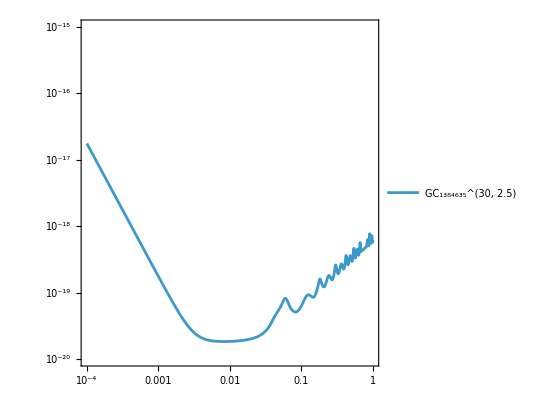

```mathematica
sensitivityFunctionPlot["path"][data[n1,"m2g-TDI"][[i1]],PlotLegends->{labelFromIndex[{n1,2.5,i1}]}]
```

## Equivalent TDI combinations

### Example of equivalent TDI combination

Import data from the combination library

```mathematica
data[16,"2g-TDI"]=Import[NotebookDirectory[]<>"data\\16-2g-TDI.txt","Lines"];
```

Plot space-time diagram

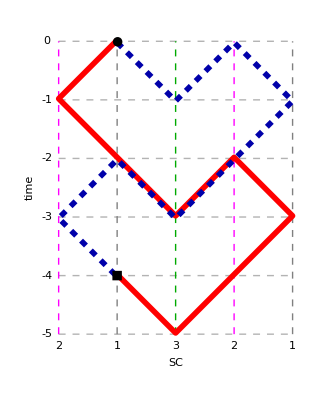

```mathematica
pa1=laserLinkTrajectoryToPath2@data[16,"2g-TDI"][[2]];
spaceTimePlot2@pa1
```

```mathematica
informationTDI@data[16,"m2g-TDI"][[2]]
```

Laser link trajectory:   1←2←1←3←2←1←2→3→1→2→1←3←2→1→2→3→1

Coordinate format:   {{{0,0},{1,-1},{0,-2},{-1,-3},{-2,-4},{-3,-5},{-2,-6},{-1,-5},{0,-4}},{{0,0},{-1,-1},{-2,-2},{-3,-3},{-2,-4},{-1,-3},{0,-2},{1,-3},{0,-4}}}

Defining formula (two virtual optical paths):   {η_1+𝒟_(33'2'1'3') η_1+𝒟_(33') η_(1')-𝒟_(33'2'1'3'3OverBar[1]'OverBar[2]') η_(1')+𝒟_3 η_(2')+𝒟_(33'2'1') η_(2')+𝒟_(33'2') η_(3')-𝒟_(33'2'1'3'3OverBar[1]') η_(3'),𝒟_(2'1'3') η_1+𝒟_(2'1'3'3OverBar[1]'OverBar[2]') η_1+η_(1')-𝒟_(2'1'3'3OverBar[1]'OverBar[2]') η_(1')+𝒟_(2'1') η_(2')+𝒟_(2'1'3'3OverBar[1]'OverBar[2]'3) η_(2')+𝒟_(2') η_(3')-𝒟_(2'1'3'3OverBar[1]') η_(3')}

Defining formula:   -((-1+𝒟_(2'1'3')+𝒟_(2'1'3'3OverBar[1]'OverBar[2]')-𝒟_(33'2'1'3')) η_1)+(-1+𝒟_(2'1'3'3OverBar[1]'OverBar[2]')+𝒟_(33')-𝒟_(33'2'1'3'3OverBar[1]'OverBar[2]')) η_(1')+(-𝒟_(2'1')-𝒟_(2'1'3'3OverBar[1]'OverBar[2]'3)+𝒟_3+𝒟_(33'2'1')) η_(2')+(-𝒟_(2')+𝒟_(2'1'3'3OverBar[1]')+𝒟_(33'2')-𝒟_(33'2'1'3'3OverBar[1]')) η_(3')

Laser noise residual:   (𝒟_(33'2'1'3'3OverBar[1]'OverBar[2]')-𝒟_(2'1'3'3OverBar[1]'OverBar[2]'33'))(ṗ)_1

Evaluation index b for the modified first-generation TDI:   {0,0,0,0,0,0}

Evaluation index d^0 for the second-generation TDI:   {0,0,0}

Evaluation index d for the modified second-generation TDI:   {0,0,0,0,0,0}

Polynomial vector format (6 variables x,y,z,l,m,n):   {1-l m n-n z+l m n^2 z,0,0,-1+2 n z-n^2 z^2,-l m+z+l m n z-n z^2,-m+2 m n z-m n^2 z^2}

Polynomial vector format (3 variables x,y,z):   {1-x y z-z^2+x y z^3,0,0,-1+2 z^2-z^4,-x y+z+x y z^2-z^3,-y+2 y z^2-y z^4}

Polynomial vector format (1 variable x):   {1-x^2-x^3+x^5,0,0,-1+2 x^2-x^4,x-x^2-x^3+x^4,-x+2 x^3-x^5}

Calculate and view the information of the TDI combination

some equivalent TDI combinations of the TDI combination

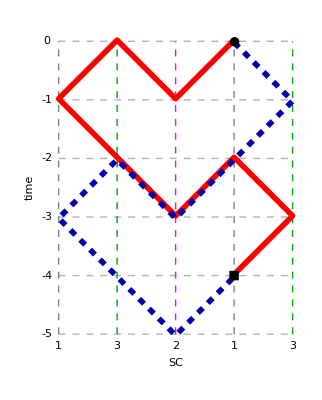
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
pa1b=pathTransform["equivalentPath"]@pa1;
spaceTimePlot2/@pa1b
```

all equivalent TDI combinations of the TDI combination

```mathematica
pa1c=pathTransform["allEquivalentPath"]@pa1;
Length@pa1c
pa1c
```

192

{1←2←1←3→2←1←2←3→1→2→1←3→2→1→2←3→1,2←1←3→2←1←2←3→1→2→1←3→2→1→2←3→1←2,1←3→2←1←2←3→1→2→1←3→2→1→2←3→1←2←1,3→2←1←2←3→1→2→1←3→2→1→2←3→1←2←1←3,2←1←2←3→1→2→1←3→2→1→2←3→1←2←1←3→2,1←2←3→1→2→1←3→2→1→2←3→1←2←1←3→2←1,2←3→1→2→1←3→2→1→2←3→1←2←1←3→2←1←2,3→1→2→1←3→2→1→2←3→1←2←1←3→2←1←2←3,1→2→1←3→2→1→2←3→1←2←1←3→2←1←2←3→1,2→1←3→2→1→2←3→1←2←1←3→2←1←2←3→1→2,1←3→2→1→2←3→1←2←1←3→2←1←2←3→1→2→1,3→2→1→2←3→1←2←1←3→2←1←2←3→1→2→1←3,2→1→2←3→1←2←1←3→2←1←2←3→1→2→1←3→2,1→2←3→1←2←1←3→2←1←2←3→1→2→1←3→2→1,2←3→1←2←1←3→2←1←2←3→1→2→1←3→2→1→2,3→1←2←1←3→2←1←2←3→1→2→1←3→2→1→2←3,2←3←2←1→3←2←3←1→2→3→2←1→3→2→3←1→2,3←2←1→3←2←3←1→2→3→2←1→3→2→3←1→2←3,2←1→3←2←3←1→2→3→2←1→3→2→3←1→2←3←2,1→3←2←3←1→2→3→2←1→3→2→3←1→2←3←2←1,3←2←3←1→2→3→2←1→3→2→3←1→2←3←2←1→3,2←3←1→2→3→2←1→3→2→3←1→2←3←2←1→3←2,3←1→2→3→2←1→3→2→3←1→2←3←2←1→3←2←3,1→2→3→2←1→3→2→3←1→2←3←2←1→3←2←3←1,2→3→2←1→3→2→3←1→2←3←2←1→3←2←3←1→2,3→2←1→3→2→3←1→2←3←2←1→3←2←3←1→2→3,2←1→3→2→3←1→2←3←2←1→3←2←3←1→2→3→2,1→3→2→3←1→2←3←2←1→3←2←3←1→2→3→2←1,3→2→3←1→2←3←2←1→3←2←3←1→2→3→2←1→3,2→3←1→2←3←2←1→3←2←3←1→2→3→2←1→3→2,3←1→2←3←2←1→3←2←3←1→2→3→2←1→3→2→3,1→2←3←2←1→3←2←3←1→2→3→2←1→3→2→3←1,3←1←3←2→1←3←1←2→3→1→3←2→1→3→1←2→3,1←3←2→1←3←1←2→3→1→3←2→1→3→1←2→3←1,3←2→1←3←1←2→3→1→3←2→1→3→1←2→3←1←3,2→1←3←1←2→3→1→3←2→1→3→1←2→3←1←3←2,1←3←1←2→3→1→3←2→1→3→1←2→3←1←3←2→1,3←1←2→3→1→3←2→1→3→1←2→3←1←3←2→1←3,1←2→3→1→3←2→1→3→1←2→3←1←3←2→1←3←1,2→3→1→3←2→1→3→1←2→3←1←3←2→1←3←1←2,3→1→3←2→1→3→1←2→3←1←3←2→1←3←1←2→3,1→3←2→1→3→1←2→3←1←3←2→1←3←1←2→3→1,3←2→1→3→1←2→3←1←3←2→1←3←1←2→3→1→3,2→1→3→1←2→3←1←3←2→1←3←1←2→3→1→3←2,1→3→1←2→3←1←3←2→1←3←1←2→3→1→3←2→1,3→1←2→3←1←3←2→1←3←1←2→3→1→3←2→1→3,1←2→3←1←3←2→1←3←1←2→3→1→3←2→1→3→1,2→3←1←3←2→1←3←1←2→3→1→3←2→1→3→1←2,1←3←1←2→3←1←3←2→1→3→1←2→3→1→3←2→1,3←1←2→3←1←3←2→1→3→1←2→3→1→3←2→1←3,1←2→3←1←3←2→1→3→1←2→3→1→3←2→1←3←1,2→3←1←3←2→1→3→1←2→3→1→3←2→1←3←1←2,3←1←3←2→1→3→1←2→3→1→3←2→1←3←1←2→3,1←3←2→1→3→1←2→3→1→3←2→1←3←1←2→3←1,3←2→1→3→1←2→3→1→3←2→1←3←1←2→3←1←3,2→1→3→1←2→3→1→3←2→1←3←1←2→3←1←3←2,1→3→1←2→3→1→3←2→1←3←1←2→3←1←3←2→1,3→1←2→3→1→3←2→1←3←1←2→3←1←3←2→1→3,1←2→3→1→3←2→1←3←1←2→3←1←3←2→1→3→1,2→3→1→3←2→1←3←1←2→3←1←3←2→1→3→1←2,3→1→3←2→1←3←1←2→3←1←3←2→1→3→1←2→3,1→3←2→1←3←1←2→3←1←3←2→1→3→1←2→3→1,3←2→1←3←1←2→3←1←3←2→1→3→1←2→3→1→3,2→1←3←1←2→3←1←3←2→1→3→1←2→3→1→3←2,2←1←2←3→1←2←1←3→2→1→2←3→1→2→1←3→2,1←2←3→1←2←1←3→2→1→2←3→1→2→1←3→2←1,2←3→1←2←1←3→2→1→2←3→1→2→1←3→2←1←2,3→1←2←1←3→2→1→2←3→1→2→1←3→2←1←2←3,1←2←1←3→2→1→2←3→1→2→1←3→2←1←2←3→1,2←1←3→2→1→2←3→1→2→1←3→2←1←2←3→1←2,1←3→2→1→2←3→1→2→1←3→2←1←2←3→1←2←1,3→2→1→2←3→1→2→1←3→2←1←2←3→1←2←1←3,2→1→2←3→1→2→1←3→2←1←2←3→1←2←1←3→2,1→2←3→1→2→1←3→2←1←2←3→1←2←1←3→2→1,2←3→1→2→1←3→2←1←2←3→1←2←1←3→2→1→2,3→1→2→1←3→2←1←2←3→1←2←1←3→2→1→2←3,1→2→1←3→2←1←2←3→1←2←1←3→2→1→2←3→1,2→1←3→2←1←2←3→1←2←1←3→2→1→2←3→1→2,1←3→2←1←2←3→1←2←1←3→2→1→2←3→1→2→1,3→2←1←2←3→1←2←1←3→2→1→2←3→1→2→1←3,3←2←3←1→2←3←2←1→3→2→3←1→2→3→2←1→3,2←3←1→2←3←2←1→3→2→3←1→2→3→2←1→3←2,3←1→2←3←2←1→3→2→3←1→2→3→2←1→3←2←3,1→2←3←2←1→3→2→3←1→2→3→2←1→3←2←3←1,2←3←2←1→3→2→3←1→2→3→2←1→3←2←3←1→2,3←2←1→3→2→3←1→2→3→2←1→3←2←3←1→2←3,2←1→3→2→3←1→2→3→2←1→3←2←3←1→2←3←2,1→3→2→3←1→2→3→2←1→3←2←3←1→2←3←2←1,3→2→3←1→2→3→2←1→3←2←3←1→2←3←2←1→3,2→3←1→2→3→2←1→3←2←3←1→2←3←2←1→3→2,3←1→2→3→2←1→3←2←3←1→2←3←2←1→3→2→3,1→2→3→2←1→3←2←3←1→2←3←2←1→3→2→3←1,2→3→2←1→3←2←3←1→2←3←2←1→3→2→3←1→2,3→2←1→3←2←3←1→2←3←2←1→3→2→3←1→2→3,2←1→3←2←3←1→2←3←2←1→3→2→3←1→2→3→2,1→3←2←3←1→2←3←2←1→3→2→3←1→2→3→2←1,1←3→2←1←2←3→1←2←1←3→2→1→2←3→1→2→1,3→2←1←2←3→1←2←1←3→2→1→2←3→1→2→1←3,2←1←2←3→1←2←1←3→2→1→2←3→1→2→1←3→2,1←2←3→1←2←1←3→2→1→2←3→1→2→1←3→2←1,2←3→1←2←1←3→2→1→2←3→1→2→1←3→2←1←2,3→1←2←1←3→2→1→2←3→1→2→1←3→2←1←2←3,1←2←1←3→2→1→2←3→1→2→1←3→2←1←2←3→1,2←1←3→2→1→2←3→1→2→1←3→2←1←2←3→1←2,1←3→2→1→2←3→1→2→1←3→2←1←2←3→1←2←1,3→2→1→2←3→1→2→1←3→2←1←2←3→1←2←1←3,2→1→2←3→1→2→1←3→2←1←2←3→1←2←1←3→2,1→2←3→1→2→1←3→2←1←2←3→1←2←1←3→2→1,2←3→1→2→1←3→2←1←2←3→1←2←1←3→2→1→2,3→1→2→1←3→2←1←2←3→1←2←1←3→2→1→2←3,1→2→1←3→2←1←2←3→1←2←1←3→2→1→2←3→1,2→1←3→2←1←2←3→1←2←1←3→2→1→2←3→1→2,2←1→3←2←3←1→2←3←2←1→3→2→3←1→2→3→2,1→3←2←3←1→2←3←2←1→3→2→3←1→2→3→2←1,3←2←3←1→2←3←2←1→3→2→3←1→2→3→2←1→3,2←3←1→2←3←2←1→3→2→3←1→2→3→2←1→3←2,3←1→2←3←2←1→3→2→3←1→2→3→2←1→3←2←3,1→2←3←2←1→3→2→3←1→2→3→2←1→3←2←3←1,2←3←2←1→3→2→3←1→2→3→2←1→3←2←3←1→2,3←2←1→3→2→3←1→2→3→2←1→3←2←3←1→2←3,2←1→3→2→3←1→2→3→2←1→3←2←3←1→2←3←2,1→3→2→3←1→2→3→2←1→3←2←3←1→2←3←2←1,3→2→3←1→2→3→2←1→3←2←3←1→2←3←2←1→3,2→3←1→2→3→2←1→3←2←3←1→2←3←2←1→3→2,3←1→2→3→2←1→3←2←3←1→2←3←2←1→3→2→3,1→2→3→2←1→3←2←3←1→2←3←2←1→3→2→3←1,2→3→2←1→3←2←3←1→2←3←2←1→3→2→3←1→2,3→2←1→3←2←3←1→2←3←2←1→3→2→3←1→2→3,3←2→1←3←1←2→3←1←3←2→1→3→1←2→3→1→3,2→1←3←1←2→3←1←3←2→1→3→1←2→3→1→3←2,1←3←1←2→3←1←3←2→1→3→1←2→3→1→3←2→1,3←1←2→3←1←3←2→1→3→1←2→3→1→3←2→1←3,1←2→3←1←3←2→1→3→1←2→3→1→3←2→1←3←1,2→3←1←3←2→1→3→1←2→3→1→3←2→1←3←1←2,3←1←3←2→1→3→1←2→3→1→3←2→1←3←1←2→3,1←3←2→1→3→1←2→3→1→3←2→1←3←1←2→3←1,3←2→1→3→1←2→3→1→3←2→1←3←1←2→3←1←3,2→1→3→1←2→3→1→3←2→1←3←1←2→3←1←3←2,1→3→1←2→3→1→3←2→1←3←1←2→3←1←3←2→1,3→1←2→3→1→3←2→1←3←1←2→3←1←3←2→1→3,1←2→3→1→3←2→1←3←1←2→3←1←3←2→1→3→1,2→3→1→3←2→1←3←1←2→3←1←3←2→1→3→1←2,3→1→3←2→1←3←1←2→3←1←3←2→1→3→1←2→3,1→3←2→1←3←1←2→3←1←3←2→1→3→1←2→3→1,1←2→3←1←3←2→1←3←1←2→3→1→3←2→1→3→1,2→3←1←3←2→1←3←1←2→3→1→3←2→1→3→1←2,3←1←3←2→1←3←1←2→3→1→3←2→1→3→1←2→3,1←3←2→1←3←1←2→3→1→3←2→1→3→1←2→3←1,3←2→1←3←1←2→3→1→3←2→1→3→1←2→3←1←3,2→1←3←1←2→3→1→3←2→1→3→1←2→3←1←3←2,1←3←1←2→3→1→3←2→1→3→1←2→3←1←3←2→1,3←1←2→3→1→3←2→1→3→1←2→3←1←3←2→1←3,1←2→3→1→3←2→1→3→1←2→3←1←3←2→1←3←1,2→3→1→3←2→1→3→1←2→3←1←3←2→1←3←1←2,3→1→3←2→1→3→1←2→3←1←3←2→1←3←1←2→3,1→3←2→1→3→1←2→3←1←3←2→1←3←1←2→3→1,3←2→1→3→1←2→3←1←3←2→1←3←1←2→3→1→3,2→1→3→1←2→3←1←3←2→1←3←1←2→3→1→3←2,1→3→1←2→3←1←3←2→1←3←1←2→3→1→3←2→1,3→1←2→3←1←3←2→1←3←1←2→3→1→3←2→1→3,2←3→1←2←1←3→2←1←2←3→1→2→1←3→2→1→2,3→1←2←1←3→2←1←2←3→1→2→1←3→2→1→2←3,1←2←1←3→2←1←2←3→1→2→1←3→2→1→2←3→1,2←1←3→2←1←2←3→1→2→1←3→2→1→2←3→1←2,1←3→2←1←2←3→1→2→1←3→2→1→2←3→1←2←1,3→2←1←2←3→1→2→1←3→2→1→2←3→1←2←1←3,2←1←2←3→1→2→1←3→2→1→2←3→1←2←1←3→2,1←2←3→1→2→1←3→2→1→2←3→1←2←1←3→2←1,2←3→1→2→1←3→2→1→2←3→1←2←1←3→2←1←2,3→1→2→1←3→2→1→2←3→1←2←1←3→2←1←2←3,1→2→1←3→2→1→2←3→1←2←1←3→2←1←2←3→1,2→1←3→2→1→2←3→1←2←1←3→2←1←2←3→1→2,1←3→2→1→2←3→1←2←1←3→2←1←2←3→1→2→1,3→2→1→2←3→1←2←1←3→2←1←2←3→1→2→1←3,2→1→2←3→1←2←1←3→2←1←2←3→1→2→1←3→2,1→2←3→1←2←1←3→2←1←2←3→1→2→1←3→2→1,3←1→2←3←2←1→3←2←3←1→2→3→2←1→3→2→3,1→2←3←2←1→3←2←3←1→2→3→2←1→3→2→3←1,2←3←2←1→3←2←3←1→2→3→2←1→3→2→3←1→2,3←2←1→3←2←3←1→2→3→2←1→3→2→3←1→2←3,2←1→3←2←3←1→2→3→2←1→3→2→3←1→2←3←2,1→3←2←3←1→2→3→2←1→3→2→3←1→2←3←2←1,3←2←3←1→2→3→2←1→3→2→3←1→2←3←2←1→3,2←3←1→2→3→2←1→3→2→3←1→2←3←2←1→3←2,3←1→2→3→2←1→3→2→3←1→2←3←2←1→3←2←3,1→2→3→2←1→3→2→3←1→2←3←2←1→3←2←3←1,2→3→2←1→3→2→3←1→2←3←2←1→3←2←3←1→2,3→2←1→3→2→3←1→2←3←2←1→3←2←3←1→2→3,2←1→3→2→3←1→2←3←2←1→3←2←3←1→2→3→2,1→3→2→3←1→2←3←2←1→3←2←3←1→2→3→2←1,3→2→3←1→2←3←2←1→3←2←3←1→2→3→2←1→3,2→3←1→2←3←2←1→3←2←3←1→2→3→2←1→3→2}

### Equivalent TDI combinations in the literature 1

M. Muratore, D. Vetrugno, S. Vitale, and O. Hartwig, Time delay interferometry combinations as instrument noise monitors for LISA, Phys. Rev. D 105, 023009 (2022)
https://doi.org/10.1103/PhysRevD.105.023009

Import TDI combinations from the literature

```mathematica
tdiMM[12]=AssociationThread[{"C_1^12","C_2^12","C_3^12"},StringReplace[#,{"→"->"←","←"->"→"}]&/@{"1→2→3→1→3→2→1←3←2←1←2←3←1","1→2→3→2→1←3←2←1→3→1←2←3←1","1→2→1←3→2←1→3←2←3→1←2→3←1"}];
tdiMM[14]=AssociationThread[{"C_1^14","C_2^14","C_3^14"},StringReplace[#,{"→"->"←","←"->"→"}]&/@{"1→2→1→3→2→1←3←2←1←2→3→1←2←3←1","1→2→1→3←2←1←3→2←1←2←3→1→2→3←1","1→2→1→3←2→1←3→2←1←2←3→1←2→3←1"}];
tdiMM[16]=AssociationThread[{"C_1^16","C_2^16","C_3^16","C_4^16","C_5^16","C_6^16","C_7^16","C_8^16","C_9^16","C_10^16","C_11^16","C_12^16","C_13^16","C_14^16","C_15^16","C_16^16","C_17^16","C_18^16","C_19^16","C_20^16","C_21^16","C_22^16","C_23^16","C_24^16","C_25^16","C_26^16","C_27^16","C_28^16"},StringReplace[#,{"→"->"←","←"->"→"}]&/@{"1→2→1→3→1→3→1→2→1←3←1←2←1←2←1←3←1","1→2→1→3→2→3→1→2→1←3←2←1←2←1←2←3←1","1→2→3→1→2→1→3→2→1←3←2←1←2←1←2←3←1","1→2→1→2→1←3←1←2←1→3→1→3→1←2←1←3←1","1→2→1→3→1→2→1←3←1←2←1→3→1←2←1←3←1","1→2→1→3→2→1→2←3←1←2←1→3→2←1←2←3←1","1→2→3→1→2→3←1←3←2←1→3→1→3←2←1←3←1","1→2→3→1→3→1→2→3←1←3←2←1→3←2←1←3←1","1→2→1→2→1←3←2←1←2→3→1→3→2←1←2←3←1","1→2→1→3→1→2→1←3←2←1←2→3→2←1←2←3←1","1→2→3→1→2→3→2→1←3←2←1→3←2←1←2←3←1","1→2→3→1→3→2→1←3←1←2←3→1→3←2←1←3←1","1→2→1→2→1←3←2←1→3→2←1←2→3→1←2←3←1","1→2→1→3→1→2→1←3→2←1←2←3←2←1←2→3←1","1→2→1→3→2←1←2←3→1→2→1←3←2←1←2→3←1","1→2→1→3←2←1←2→3→2←1←2←3→1→2→1←3←1","1→2→1→3→2←1←3←2←1→3→1→2←3←1←2→3←1","1→2→1→3←2←1→3→2→1←3←1←2→3→1←2←3←1","1→2→3→2→3→2→1←3←2←1→3←2←3→1←2←3←1","1→2→3→2→3→2→1←3←2←3→1←2←1→3←2←3←1","1→2→1→2→3←1←2←1→3←2→1→3←2←1←2→3←1","1→2→1→3←2←1←2→3←1←2←1→3←2→1→2→3←1","1→2→1→2→1←3→2←1←2←3→1→3←2←1←2→3←1","1→2→3→1←2←1→3←2←1→3→2→1←3←1→2←3←1","1→2→3→2→1←3←2←3→1←2→3→2←1→3←2←3←1","1→2→1→2→1←3→2←1→3←2←1←2←3→1←2→3←1","1→2→1→3→2←1→3←2→1←3←1←2←3→1←2→3←1","1→2→1←3←2→1←3→2←1→3→1←2←3→1←2→3←1"}];
```

Import TDI combinations from the library GTDI

```mathematica
data[12,"2g-TDI"]=Import[NotebookDirectory[]<>"data\\12-2g-TDI.txt","Lines"];
data[14,"2g-TDI"]=Import[NotebookDirectory[]<>"data\\14-2g-TDI.txt","Lines"];
data[16,"2g-TDI"]=Import[NotebookDirectory[]<>"data\\16-2g-TDI.txt","Lines"];
```

Except for three combinations (C_4^16, C_24^16, C_28^16) that are not sensitive to gravitational waves, all other TDI combinations are equivalent to the combinations in the library GTDI

```mathematica
equivalentPathSixIndex[#,data[12,"2g-TDI"]]&/@tdiMM[12]
markFromIndex[Insert[#[[1]],2,2],#[[2]]]&/@%//Normal//Column
```

<|C_1^12→{{12,1},{0,0,0,0}},C_2^12→{{12,2},{0,0,0,0}},C_3^12→{{12,3},{0,0,0,0}}|>

C_1^12→GC_(1,0,0,0,0)^(12,2)
C_2^12→GC_(2,0,0,0,0)^(12,2)
C_3^12→GC_(3,0,0,0,0)^(12,2)

```mathematica
equivalentPathSixIndex[#,data[14,"2g-TDI"]]&/@tdiMM[14]
markFromIndex[Insert[#[[1]],2,2],#[[2]]]&/@%//Normal//Column
```

<|C_1^14→{{14,4},{0,0,0,0}},C_2^14→{{14,2},{1,1,2,4}},C_3^14→{{14,3},{1,1,2,4}}|>

C_1^14→GC_(4,0,0,0,0)^(14,2)
C_2^14→GC_(2,1,1,2,4)^(14,2)
C_3^14→GC_(3,1,1,2,4)^(14,2)

```mathematica
pSet[16,"2g"]=pathTransform["firstInAllEquivalentPath"]/@data[16,"2g-TDI"];
```

```mathematica
equivalentPathSixIndex[#,data[16,"2g-TDI"],pSet[16,"2g"]]&/@tdiMM[16]
If[Head[#]===String,#,markFromIndex[Insert[#[[1]],2,2],#[[2]]]]&/@%//Normal//Column
```

<|C_1^16→{{16,27},{0,0,0,0}},C_2^16→{{16,26},{0,0,0,0}},C_3^16→{{16,25},{0,0,0,0}},C_4^16→unequivalence,C_5^16→{{16,4},{0,0,0,0}},C_6^16→{{16,3},{0,0,0,0}},C_7^16→{{16,31},{1,1,0,0}},C_8^16→{{16,35},{1,1,0,0}},C_9^16→{{16,24},{0,0,0,0}},C_10^16→{{16,19},{0,0,0,0}},C_11^16→{{16,14},{1,1,0,0}},C_12^16→{{16,5},{1,1,0,0}},C_13^16→{{16,32},{0,0,0,0}},C_14^16→{{16,15},{0,0,0,0}},C_15^16→{{16,12},{0,0,0,0}},C_16^16→{{16,7},{0,0,2,5}},C_17^16→{{16,38},{0,0,0,0}},C_18^16→{{16,36},{0,0,0,0}},C_19^16→{{16,17},{0,0,0,0}},C_20^16→{{16,18},{0,0,0,0}},C_21^16→{{16,37},{1,1,1,2}},C_22^16→{{16,2},{0,1,1,4}},C_23^16→{{16,1},{1,1,1,2}},C_24^16→unequivalence,C_25^16→{{16,9},{0,0,0,0}},C_26^16→{{16,29},{1,1,2,4}},C_27^16→{{16,16},{1,1,2,4}},C_28^16→unequivalence|>

C_1^16→GC_(27,0,0,0,0)^(16,2)
C_2^16→GC_(26,0,0,0,0)^(16,2)
C_3^16→GC_(25,0,0,0,0)^(16,2)
C_4^16→unequivalence
C_5^16→GC_(4,0,0,0,0)^(16,2)
C_6^16→GC_(3,0,0,0,0)^(16,2)
C_7^16→GC_(31,1,1,0,0)^(16,2)
C_8^16→GC_(35,1,1,0,0)^(16,2)
C_9^16→GC_(24,0,0,0,0)^(16,2)
C_10^16→GC_(19,0,0,0,0)^(16,2)
C_11^16→GC_(14,1,1,0,0)^(16,2)
C_12^16→GC_(5,1,1,0,0)^(16,2)
C_13^16→GC_(32,0,0,0,0)^(16,2)
C_14^16→GC_(15,0,0,0,0)^(16,2)
C_15^16→GC_(12,0,0,0,0)^(16,2)
C_16^16→GC_(7,0,0,2,5)^(16,2)
C_17^16→GC_(38,0,0,0,0)^(16,2)
C_18^16→GC_(36,0,0,0,0)^(16,2)
C_19^16→GC_(17,0,0,0,0)^(16,2)
C_20^16→GC_(18,0,0,0,0)^(16,2)
C_21^16→GC_(37,1,1,1,2)^(16,2)
C_22^16→GC_(2,0,1,1,4)^(16,2)
C_23^16→GC_(1,1,1,1,2)^(16,2)
C_24^16→unequivalence
C_25^16→GC_(9,0,0,0,0)^(16,2)
C_26^16→GC_(29,1,1,2,4)^(16,2)
C_27^16→GC_(16,1,1,2,4)^(16,2)
C_28^16→unequivalence

### Equivalent TDI combinations in the literature 2

Wang Pan-Pan et al., Sensitivity functions for geometric time-delay interferometry combinations, Phys. Rev. D 108, 044075 (2023)
https://doi.org/10.1103/PhysRevD.108.044075

Import TDI combinations from the literature

```mathematica
tdiW[12]=<|"[α]_1^12"->"1←2←3←1←3←2←1→3→2→1→2→3→1","[α]_2^12"->"1←2←3←2←1→3→2→1←3←1→2→3→1","[α]_3^12"->"1←2←1→3←2→1←3→2→3←1→2←3→1"|>;
tdiW[14]=<|"[U]_1^14"->"1←2←1←3←2←1→3→2→1→2←3←1→2→3→1","[U]_2^14"->"1←2←3←1←3→2→1←3←2←1→3→1→2→3→1","[EP]_1^14"->"1←2←3←2→1←3←2←1→3→2→3←1→2→3→1","[EP]_2^14"->"1←2←1←3→2←1→3←2→1→2→3←1→2←3→1"|>;
tdiW[16]=Union[<|"[X]_1^16"->"1←2←1←3←1←3←1←2←1→3→1→2→1→2→1→3→1","[X]_2^16"->"1←2←1←3←1←2←1→3→1→2→1←3←1→2→1→3→1","[U]_1^16"->"1←2←1←3←2→1←3←2←1←2→3→1→2→1→2→3→1","[U]_2^16"->"1←2←1←3←2←1←2→3→1→2→1←3←2→1→2→3→1","[U]_3^16"->"1←2←1←3←2→1→2→1←3←2←1←2→3→1→2→3→1","[E]_1^16"->"1←2←3←2→1←3←2←3→1←2→3→2→1←3→2→3→1","[E]_2^16"->"1←2←3←2←3→1←2→3→2→1←3←2→1←3→2→3→1","[P]_1^16"->"1←2←1←3→2←1←2←3→1→2→1←3→2→1→2←3→1","[P]_2^16"->"1←2←1←3→2→1←3→2←1←2←3→1→2→1→2←3→1"|>,<|"[U]_4^16"->"1←2←1←3←2←3←1←2←1→3→2→1→2→1→2→3→1","[U]_5^16"->"1←2←1←3←2→1→2←3←1←2←1→3→2→1→2→3→1","[U]_6^16"->"1←2←1←3←1←2←1→3→2→1→2←3←2→1→2→3→1","[PE]_1^16"->"1←2←3←2←1→3→2→3←1→2←3←2→1←3→2→3→1","[PE]_2^16"->"1←2←3←2→1→2←3←2←1→3→2→3←1←3→2→3→1","[PE]_3^16"->"1←2←3←2←3←2←1→3→2→3←1→2→1←3→2→3→1","[PE]_4^16"->"1←2←1←3←1←2←1→3←2→1→2→3→2→1→2←3→1","[PE]_5^16"->"1←2←1←3←2→1→2→1→2←3←1←2←1→3→2→3→1","[PE]_6^16"->"1←2←1←3←2→1→2→3←1←2←1→3→2→1→2←3→1","[PE]_7^16"->"1←2←1←3→2→1→2←3←1←2←1→3←2→1→2→3→1","[PE]_8^16"->"1←2←1←3→2→3←1←2←1→3←2→1→2→1→2←3→1","[PE]_9^16"->"1←2←1←2←1→3→2→3←1←3←2→1→2→1→2←3→1","[PE]_10^16"->"1←2←1←2←1→3←2→1→2→1→2←3←1←3→2→3→1"|>,<|"[T]_1^16"->"1←2←1←3→2→1←3←2←1→3→1→2←3←1→2→3→1","[T]_2^16"->"1←2←1←2←1→3→2→1←3←2→1→2←3←1→2→3→1","[T]_3^16"->"1←2←3←2←1←3←2←1→3→2→1→2→3←1→2→3→1","[T]_4^16"->"1←2←3←2←1→3←2→1→2→1←3←1←2→3→2→3→1","[T]_5^16"->"1←2←3←2←3←2←1→3→2→1←3→2→3←1→2→3→1","[T]_6^16"->"1←2←3←1←3←2→1←3←2←1→3→2→3→1→2→3→1","[T]_7^16"->"1←2←3←1←3←1←3←2←1→3→2→1→3→1→2→3→1","[T]_8^16"->"1←2←3←1←3→2←1→3→2→1←3←2←3→1→2→3→1","[T]_9^16"->"1←2←1←2→3→2→1←3←2→1←3←1→2←3→1→3→1","[T]_11^16"->"1←2←1←3←2→1→3→2→1←3←1←2→3→1→2←3→1","[T]_12^16"->"1←2←1←3←2→1←3→2←1→3→1→2→3←1→2←3→1","[T]_14^16"->"1←2←1←3→2→1←3→2→3←1→2←3←2←3→1→3→1","[T]_15^16"->"1←2←1←2←1→3←2→1←3→2→1→2→3←1→2←3→1","[T]_16^16"->"1←2←1←2←3→1→2→1→3←2→1←3←1←3→2→3→1","[T]_18^16"->"1←2←1→3←2→1→2←3←2→1←3→2→3←1←2→3→1","[T]_19^16"->"1←2←1→3→2←1←3→2→3←1→2←3←2→1→2←3→1"|>];
```

Import TDI combinations from the library GTDI

```mathematica
data[12,"2g-TDI"]=Import[NotebookDirectory[]<>"data\\12-2g-TDI.txt","Lines"];
data[14,"2g-TDI"]=Import[NotebookDirectory[]<>"data\\14-2g-TDI.txt","Lines"];
data[16,"2g-TDI"]=Import[NotebookDirectory[]<>"data\\16-2g-TDI.txt","Lines"];
```

All TDI combinations are equivalent to the combinations in the library GTDI

```mathematica
equivalentPathSixIndex[#,data[12,"2g-TDI"]]&/@tdiW[12]
markFromIndex[Insert[#[[1]],2,2],#[[2]]]&/@%//Normal//Column
```

<|[α]_1^12→{{12,1},{0,0,0,0}},[α]_2^12→{{12,2},{0,0,0,0}},[α]_3^12→{{12,3},{0,0,0,0}}|>

[α]_1^12→GC_(1,0,0,0,0)^(12,2)
[α]_2^12→GC_(2,0,0,0,0)^(12,2)
[α]_3^12→GC_(3,0,0,0,0)^(12,2)

```mathematica
equivalentPathSixIndex[#,data[14,"2g-TDI"]]&/@tdiW[14]
markFromIndex[Insert[#[[1]],2,2],#[[2]]]&/@%//Normal//Column
```

<|[U]_1^14→{{14,4},{0,0,0,0}},[U]_2^14→{{14,1},{0,0,0,0}},[EP]_1^14→{{14,2},{0,0,0,0}},[EP]_2^14→{{14,3},{1,1,2,4}}|>

[U]_1^14→GC_(4,0,0,0,0)^(14,2)
[U]_2^14→GC_(1,0,0,0,0)^(14,2)
[EP]_1^14→GC_(2,0,0,0,0)^(14,2)
[EP]_2^14→GC_(3,1,1,2,4)^(14,2)

```mathematica
pSet[16,"2g"]=pathTransform["firstInAllEquivalentPath"]/@data[16,"2g-TDI"];
```

```mathematica
equivalentPathSixIndex[#,data[16,"2g-TDI"],pSet[16,"2g"]]&/@tdiW[16]
markFromIndex[Insert[#[[1]],2,2],#[[2]]]&/@%//Normal//Column
```

<|[X]_1^16→{{16,27},{0,0,0,0}},[X]_2^16→{{16,4},{0,0,0,0}},[U]_1^16→{{16,35},{0,0,0,0}},[U]_2^16→{{16,3},{0,0,0,0}},[U]_3^16→{{16,31},{0,0,0,0}},[E]_1^16→{{16,6},{0,0,0,0}},[E]_2^16→{{16,30},{1,1,0,0}},[P]_1^16→{{16,2},{0,0,0,0}},[P]_2^16→{{16,37},{0,0,0,0}},[U]_4^16→{{16,26},{0,0,0,0}},[U]_5^16→{{16,5},{0,0,0,0}},[U]_6^16→{{16,19},{0,0,0,0}},[PE]_1^16→{{16,9},{0,0,0,0}},[PE]_2^16→{{16,7},{0,0,0,0}},[PE]_3^16→{{16,18},{0,0,0,0}},[PE]_4^16→{{16,15},{0,0,0,0}},[PE]_5^16→{{16,24},{1,1,1,8}},[PE]_6^16→{{16,12},{0,0,0,0}},[PE]_7^16→{{16,13},{0,0,0,0}},[PE]_8^16→{{16,1},{0,0,0,0}},[PE]_9^16→{{16,10},{0,0,0,0}},[PE]_10^16→{{16,21},{0,0,0,0}},[T]_1^16→{{16,36},{0,0,0,0}},[T]_2^16→{{16,32},{0,0,0,0}},[T]_3^16→{{16,28},{0,0,0,0}},[T]_4^16→{{16,23},{0,0,0,0}},[T]_5^16→{{16,17},{0,0,0,0}},[T]_6^16→{{16,14},{0,0,0,0}},[T]_7^16→{{16,25},{1,1,0,0}},[T]_8^16→{{16,20},{0,0,0,0}},[T]_9^16→{{16,11},{0,1,0,10}},[T]_11^16→{{16,38},{0,0,0,0}},[T]_12^16→{{16,16},{1,1,2,4}},[T]_14^16→{{16,33},{1,1,2,8}},[T]_15^16→{{16,29},{1,1,2,4}},[T]_16^16→{{16,8},{0,1,0,6}},[T]_18^16→{{16,22},{0,0,0,0}},[T]_19^16→{{16,34},{0,0,0,0}}|>

[X]_1^16→GC_(27,0,0,0,0)^(16,2)
[X]_2^16→GC_(4,0,0,0,0)^(16,2)
[U]_1^16→GC_(35,0,0,0,0)^(16,2)
[U]_2^16→GC_(3,0,0,0,0)^(16,2)
[U]_3^16→GC_(31,0,0,0,0)^(16,2)
[E]_1^16→GC_(6,0,0,0,0)^(16,2)
[E]_2^16→GC_(30,1,1,0,0)^(16,2)
[P]_1^16→GC_(2,0,0,0,0)^(16,2)
[P]_2^16→GC_(37,0,0,0,0)^(16,2)
[U]_4^16→GC_(26,0,0,0,0)^(16,2)
[U]_5^16→GC_(5,0,0,0,0)^(16,2)
[U]_6^16→GC_(19,0,0,0,0)^(16,2)
[PE]_1^16→GC_(9,0,0,0,0)^(16,2)
[PE]_2^16→GC_(7,0,0,0,0)^(16,2)
[PE]_3^16→GC_(18,0,0,0,0)^(16,2)
[PE]_4^16→GC_(15,0,0,0,0)^(16,2)
[PE]_5^16→GC_(24,1,1,1,8)^(16,2)
[PE]_6^16→GC_(12,0,0,0,0)^(16,2)
[PE]_7^16→GC_(13,0,0,0,0)^(16,2)
[PE]_8^16→GC_(1,0,0,0,0)^(16,2)
[PE]_9^16→GC_(10,0,0,0,0)^(16,2)
[PE]_10^16→GC_(21,0,0,0,0)^(16,2)
[T]_1^16→GC_(36,0,0,0,0)^(16,2)
[T]_2^16→GC_(32,0,0,0,0)^(16,2)
[T]_3^16→GC_(28,0,0,0,0)^(16,2)
[T]_4^16→GC_(23,0,0,0,0)^(16,2)
[T]_5^16→GC_(17,0,0,0,0)^(16,2)
[T]_6^16→GC_(14,0,0,0,0)^(16,2)
[T]_7^16→GC_(25,1,1,0,0)^(16,2)
[T]_8^16→GC_(20,0,0,0,0)^(16,2)
[T]_9^16→GC_(11,0,1,0,10)^(16,2)
[T]_11^16→GC_(38,0,0,0,0)^(16,2)
[T]_12^16→GC_(16,1,1,2,4)^(16,2)
[T]_14^16→GC_(33,1,1,2,8)^(16,2)
[T]_15^16→GC_(29,1,1,2,4)^(16,2)
[T]_16^16→GC_(8,0,1,0,6)^(16,2)
[T]_18^16→GC_(22,0,0,0,0)^(16,2)
[T]_19^16→GC_(34,0,0,0,0)^(16,2)